### Start choosing the example:

```mathematica
t="Jamaratv9";
beta =0;
A = 0.2;
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/Examples/ExamplesParameters.m"];
g[x];
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t];
```

```mathematica
Data
```

<|Vertices List→{1,2,3,4,5,6,7,8,9},Adjacency Matrix→{{0,1,1,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0},{0,0,0,1,1,0,0,0,0},{0,0,0,0,0,1,0,0,0},{0,0,0,0,0,1,1,0,0},{0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0}},Entrance Vertices and Currents→{{1,I1},{2,I2}},Exit Vertices and Terminal Costs→{{7,U1},{8,U2},{9,U3}},Switching Costs→{}|>

### Look at the output bellow before trying to rerun!

```mathematica
(*With U2->2, agents don't exit through 6. running with U2->U2 to determine the largest value for which we get some current, hence unicity.*)
```

```mathematica
(rule=CriticalCongestionSolver2[d2e=D2E[Data/.{I1-> 130,I2->(*129*)(*20*)129, U1-> 20,U2->100,U3->0}]])//AbsoluteTiming(*does not get all us in the first "step"*)
```

Variables are all set

Assembled most elements of the system

CleanEqualities for the switching conditions on each vertex

CleanEqualities for the complementary conditions (given the rules)

CleanEqualities for the values at the auxiliary edges

CleanEqualities for the balance conditions in terms of (mostly) transition currents

CleanEqualities for the (non) critical case equations

EliminateVarsSimplify for the us

Finished with the us!

Finish with the js

{0.374753,<|u1→18356/41,u2→18421/41,u3→18356/41,u4→12961/41,u5→18421/41,u6→13197/41,u7→12961/41,u8→13197/41,u9→12961/41,u10→7330/41,u11→13197/41,u12→8209/41,u13→7330/41,u14→8209/41,u15→7330/41,u16→20,u17→8209/41,u18→100,u19→20,u20→0,u21→20,u22→20,u23→100,u24→0,u25→100,u26→100,u27→0,u28→0,u29→18356/41,u30→18356/41,u31→18421/41,u32→18421/41,j1→65/41,j2→0,j3→0,j4→5395/41,j5→0,j6→5224/41,j7→236/41,j8→0,j9→0,j10→5631/41,j11→0,j12→4988/41,j13→879/41,j14→0,j15→0,j16→6510/41,j17→0,j18→4109/41,j19→0,j20→20,j21→0,j22→5690/41,j23→0,j24→100,j25→0,j26→9/41,j27→0,j28→120,j29→0,j30→130,j31→0,j32→129|>}

```mathematica
Keys@d2e
```

{Vertices List,Adjacency Matrix,Entrance Vertices and Currents,Exit Vertices and Terminal Costs,Switching Costs,BG,InEdges,OutEdges,FG,jvars,jtvars,uvars,costpluscurrents,jays,AllOr,AllIneq,EqPosJs,EqCurrentCompCon,EqTransitionCompCon,EqAllAll,BoundaryRules,InitRules,RulesCriticalCase,RulesCriticalCase1,RuleEntryIn,Nlhs,MinimalTimeRhs,EqCriticalCase,EqNonCritical,RuleNonCritical,RuleNonCritical1,EqSwitchingConditions,EqValueAuxiliaryEdges,EqBalanceSplittingCurrents,EqBalanceGatheringCurrents,Nrhs}

```mathematica
d2e["RuleNonCritical"]
```

<|j2→-jt12+jt19+jt20,j4→jt13+jt14,j29→0,j1→-131/4-cpc1/4+cpc2/4-cpc3/4+cpc4/4-jt12+jt14/4+jt16/4-jt17/4-jt18/4+jt19+jt20,j6→jt19+jt20,j31→0,j3→-389/4+cpc1/4-cpc2/4+cpc3/4-cpc4/4+jt13+(3 jt14)/4-jt16/4+jt17/4+jt18/4,j8→jt13+jt18,j10→jt14+jt16,j5→-647/4-cpc1/4+cpc2/4-cpc3/4+cpc4/4+jt14/4+jt16/4-jt17/4-jt18/4+jt19+jt20,j7→-389/4+cpc1/4-cpc2/4+cpc3/4-cpc4/4+jt13+(3 jt14)/4+(3 jt16)/4-(3 jt17)/4+jt18/4,j12→jt20+jt22,j9→jt17+jt18,j14→1425/4-cpc1/4+cpc2/4-cpc3/4-(3 cpc4)/4+cpc5-cpc6+cpc7-(11 jt14)/4-(11 jt16)/4+(15 jt17)/4+(15 jt18)/4+jt28-jt29,j16→jt14+jt16-jt25+jt28,j11→-259+jt14+jt16-jt17-jt18+jt20+jt22,j13→jt17+jt18+jt28-jt29,j18→jt32+jt34,j15→1425/4-cpc1/4+cpc2/4-cpc3/4-(3 cpc4)/4+cpc5-cpc6+cpc7-(11 jt14)/4-(11 jt16)/4+(15 jt17)/4+(15 jt18)/4-jt25+jt28,j20→jt37,j22→-9197/4+(5 cpc1)/4-cpc10+cpc11-(5 cpc2)/4+(5 cpc3)/4+(15 cpc4)/4-5 cpc5+5 cpc6-4 cpc7-cpc8+cpc9+(71 jt14)/4+(71 jt16)/4-(71 jt17)/4-(71 jt18)/4+jt32+jt34-jt43+jt46,j17→-2461/4+cpc1/4-cpc2/4+cpc3/4+(3 cpc4)/4-cpc5+cpc6-cpc7+(15 jt14)/4+(15 jt16)/4-(15 jt17)/4-(15 jt18)/4+jt32+jt34,j24→jt43,j26→jt32+jt34-jt43+jt46,j19→-1943+cpc1-cpc10+cpc11-cpc2+cpc3+3 cpc4-4 cpc5+4 cpc6-3 cpc7-cpc8+cpc9+14 jt14+14 jt16-14 jt17-14 jt18+jt32+jt34+jt37-jt43+jt46,j23→-2461/4+cpc1/4-cpc2/4+cpc3/4+(3 cpc4)/4-cpc5+cpc6-cpc7+(15 jt14)/4+(15 jt16)/4-(15 jt17)/4-(15 jt18)/4+jt32+jt34+jt46,j28→10233/4-(5 cpc1)/4+cpc10-cpc11+(5 cpc2)/4-(5 cpc3)/4-(15 cpc4)/4+5 cpc5-5 cpc6+4 cpc7+cpc8-cpc9-(71 jt14)/4-(71 jt16)/4+(71 jt17)/4+(71 jt18)/4-2 jt32-2 jt34+2 jt43-2 jt46,j30→130,j32→129,u22→20,u26→100,u28→0,u3→u1,u5→-131/4+(3 cpc1)/4+cpc2/4-cpc3/4+cpc4/4+jt14/4+jt16/4-jt17/4-jt18/4+u1,u7→-389/4+cpc1/4+(3 cpc2)/4+cpc3/4-cpc4/4-jt14/4-jt16/4+jt17/4+jt18/4+u1,u9→-389/4+cpc1/4+(3 cpc2)/4+cpc3/4-cpc4/4-jt14/4-jt16/4+jt17/4+jt18/4+u1,u6→-389/2+cpc1/2+cpc2/2+cpc3/2+cpc4/2+jt14/2+jt16/2-jt17/2-jt18/2+u1,u8→-389/2+cpc1/2+cpc2/2+cpc3/2+cpc4/2+jt14/2+jt16/2-jt17/2-jt18/2+u1,u13→-389/4+cpc1/4+(3 cpc2)/4+cpc3/4-cpc4/4+cpc5-(5 jt14)/4-(5 jt16)/4+(5 jt17)/4+(5 jt18)/4+u1,u15→-389/4+cpc1/4+(3 cpc2)/4+cpc3/4-cpc4/4+cpc5-(5 jt14)/4-(5 jt16)/4+(5 jt17)/4+(5 jt18)/4+u1,u14→-907/2+cpc1/2+cpc2/2+cpc3/2+cpc4/2+cpc6+(3 jt14)/2+(3 jt16)/2-(3 jt17)/2-(3 jt18)/2+u1,u17→-907/2+cpc1/2+cpc2/2+cpc3/2+cpc4/2+cpc6+(3 jt14)/2+(3 jt16)/2-(3 jt17)/2-(3 jt18)/2+u1,u19→259+cpc2-cpc4+2 cpc5-cpc6+cpc7+cpc8-5 jt14-5 jt16+5 jt17+5 jt18+u1,u23→-4275/4+(3 cpc1)/4+cpc2/4+(3 cpc3)/4+(5 cpc4)/4-cpc5+2 cpc6-cpc7+cpc9+(21 jt14)/4+(21 jt16)/4-(21 jt17)/4-(21 jt18)/4+u1,u24→-1684+cpc1+cpc11+cpc3+2 cpc4-2 cpc5+3 cpc6-2 cpc7+cpc9+9 jt14+9 jt16-9 jt17-9 jt18+jt32+jt34-jt43+jt46+u1,jt10→0,jt2→0,jt4→0,jt41→0,jt42→0,jt47→0,jt48→0,jt53→0,jt54→0,jt8→0,u21→20,u25→100,u27→0,u30→u29,u32→u31,j21→0,j25→0,j27→0,jt1→-131/4-cpc1/4+cpc2/4-cpc3/4+cpc4/4-jt12+jt14/4+jt16/4-jt17/4-jt18/4+jt19+jt20,jt11→129-jt12,jt15→-389/4+cpc1/4-cpc2/4+cpc3/4-cpc4/4+jt13+(3 jt14)/4-jt16/4-(3 jt17)/4+jt18/4,jt21→jt13+jt18-jt22,jt24→-389/4+cpc1/4-cpc2/4+cpc3/4-cpc4/4+jt13+(3 jt14)/4+(3 jt16)/4-(3 jt17)/4+jt18/4-jt19,jt26→jt14+jt16-jt25,jt27→jt17+jt18-jt29,jt3→-389/4+cpc1/4-cpc2/4+cpc3/4-cpc4/4+jt13+(3 jt14)/4-jt16/4+jt17/4+jt18/4,jt30→1425/4-cpc1/4+cpc2/4-cpc3/4-(3 cpc4)/4+cpc5-cpc6+cpc7-(11 jt14)/4-(11 jt16)/4+(15 jt17)/4+(15 jt18)/4-jt25+jt28-jt29,jt31→jt20+jt22-jt32,jt33→1425/4-cpc1/4+cpc2/4-cpc3/4-(3 cpc4)/4+cpc5-cpc6+cpc7-(11 jt14)/4-(11 jt16)/4+(15 jt17)/4+(15 jt18)/4+jt28-jt29-jt34,jt35→-2461/4+cpc1/4-cpc2/4+cpc3/4+(3 cpc4)/4-cpc5+cpc6-cpc7+(15 jt14)/4+(15 jt16)/4-(19 jt17)/4-(19 jt18)/4+jt20+jt22-jt28+jt29+jt34,jt36→jt17+jt18-jt20-jt22+jt28-jt29+jt32,jt38→jt14+jt16-jt25+jt28-jt37,jt40→-9197/4+(5 cpc1)/4-cpc10+cpc11-(5 cpc2)/4+(5 cpc3)/4+(15 cpc4)/4-5 cpc5+5 cpc6-4 cpc7-cpc8+cpc9+(67 jt14)/4+(67 jt16)/4-(71 jt17)/4-(71 jt18)/4+jt25-jt28+jt32+jt34+jt37-jt43+jt46,jt44→jt32+jt34-jt43,jt45→-2461/4+cpc1/4-cpc2/4+cpc3/4+(3 cpc4)/4-cpc5+cpc6-cpc7+(15 jt14)/4+(15 jt16)/4-(15 jt17)/4-(15 jt18)/4+jt32+jt34,jt49→-2461/4+cpc1/4-cpc2/4+cpc3/4+(3 cpc4)/4-cpc5+cpc6-cpc7+(15 jt14)/4+(15 jt16)/4-(15 jt17)/4-(15 jt18)/4+jt32+jt34+jt46,jt5→389/4-cpc1/4+cpc2/4-cpc3/4+cpc4/4-jt12-jt13-(3 jt14)/4+jt16/4-jt17/4-jt18/4+jt19+jt20,jt50→2461/4-cpc1/4+cpc2/4-cpc3/4-(3 cpc4)/4+cpc5-cpc6+cpc7-(15 jt14)/4-(15 jt16)/4+(15 jt17)/4+(15 jt18)/4-jt32-jt34+jt37-jt46,jt52→1943-cpc1+cpc10-cpc11+cpc2-cpc3-3 cpc4+4 cpc5-4 cpc6+3 cpc7+cpc8-cpc9-14 jt14-14 jt16+14 jt17+14 jt18-jt32-jt34-jt37+2 jt43-jt46,jt6→131/4+cpc1/4-cpc2/4+cpc3/4-cpc4/4+jt12+jt13+(3 jt14)/4-jt16/4+jt17/4+jt18/4-jt19-jt20,jt7→-jt12+jt19+jt20,jt9→-647/4-cpc1/4+cpc2/4-cpc3/4+cpc4/4+jt14/4+jt16/4-jt17/4-jt18/4+jt19+jt20,jt23→-647/4-cpc1/4+cpc2/4-cpc3/4+cpc4/4-jt13+jt14/4+jt16/4-jt17/4-(5 jt18)/4+jt19+jt20+jt22,jt39→1425/4-cpc1/4+cpc2/4-cpc3/4-(3 cpc4)/4+cpc5-cpc6+cpc7-(11 jt14)/4-(11 jt16)/4+(15 jt17)/4+(15 jt18)/4-jt25+jt28,jt51→-1943+cpc1-cpc10+cpc11-cpc2+cpc3+3 cpc4-4 cpc5+4 cpc6-3 cpc7-cpc8+cpc9+14 jt14+14 jt16-14 jt17-14 jt18+jt32+jt34+jt37-jt43+jt46,u10→-389/4+cpc1/4+(3 cpc2)/4+cpc3/4-cpc4/4+cpc5-(5 jt14)/4-(5 jt16)/4+(5 jt17)/4+(5 jt18)/4+u1,u11→-389/2+cpc1/2+cpc2/2+cpc3/2+cpc4/2+jt14/2+jt16/2-jt17/2-jt18/2+u1,u12→-907/2+cpc1/2+cpc2/2+cpc3/2+cpc4/2+cpc6+(3 jt14)/2+(3 jt16)/2-(3 jt17)/2-(3 jt18)/2+u1,u16→259+cpc2-cpc4+2 cpc5-cpc6+cpc7+cpc8-5 jt14-5 jt16+5 jt17+5 jt18+u1,u18→-4275/4+(3 cpc1)/4+cpc2/4+(3 cpc3)/4+(5 cpc4)/4-cpc5+2 cpc6-cpc7+cpc9+(21 jt14)/4+(21 jt16)/4-(21 jt17)/4-(21 jt18)/4+u1,u2→-131/4+(3 cpc1)/4+cpc2/4-cpc3/4+cpc4/4+jt14/4+jt16/4-jt17/4-jt18/4+u1,u20→-1684+cpc1+cpc11+cpc3+2 cpc4-2 cpc5+3 cpc6-2 cpc7+cpc9+9 jt14+9 jt16-9 jt17-9 jt18+jt32+jt34-jt43+jt46+u1,u4→-389/4+cpc1/4+(3 cpc2)/4+cpc3/4-cpc4/4-jt14/4-jt16/4+jt17/4+jt18/4+u1|>

### Non-critical congestion

```mathematica
Cost[current_,edge_]
```

IntM[current_,edge_]

```mathematica
Cost[a_,b_]:= -a
```

```mathematica
Cost[a_,b_]:= 0
```

```mathematica
d2e=D2E[Data/.{I1-> 130,I2->(*129*)(*20*)129, U1-> 20,U2->100,U3->0}];
```

Variables are all set

Assembled most elements of the system

CleanEqualities for the switching conditions on each vertex

CleanEqualities for the complementary conditions (given the rules)

CleanEqualities for the values at the auxiliary edges

CleanEqualities for the balance conditions in terms of (mostly) transition currents

CleanEqualities for the (non) critical case equations

```mathematica
alpha =0.2;
FFR=FixedPoint[FixedReduce2[d2e],<||>,1]//AbsoluteTiming
```

EliminateVarsSimplify for the us

Finished with the us!

Finish with the js

{0.122322,<|u1→18356/41,u2→18421/41,u3→18356/41,u4→12961/41,u5→18421/41,u6→13197/41,u7→12961/41,u8→13197/41,u9→12961/41,u10→7330/41,u11→13197/41,u12→8209/41,u13→7330/41,u14→8209/41,u15→7330/41,u16→20,u17→8209/41,u18→100,u19→20,u20→0,u21→20,u22→20,u23→100,u24→0,u25→100,u26→100,u27→0,u28→0,u29→18356/41,u30→18356/41,u31→18421/41,u32→18421/41,j1→65/41,j2→0,j3→0,j4→5395/41,j5→0,j6→5224/41,j7→236/41,j8→0,j9→0,j10→5631/41,j11→0,j12→4988/41,j13→879/41,j14→0,j15→0,j16→6510/41,j17→0,j18→4109/41,j19→0,j20→20,j21→0,j22→5690/41,j23→0,j24→100,j25→0,j26→9/41,j27→0,j28→120,j29→0,j30→130,j31→0,j32→129|>}

```mathematica
jsys=(d2e["EqCriticalCase"]/. uvalues)&&d2e["EqPosJs"]&&d2e["EqCurrentCompCon"];FFR
```

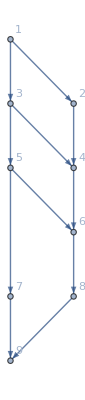
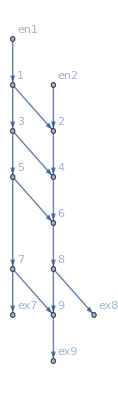
<|Vertices List→{1,2,3,4,5,6,7,8,9},Adjacency Matrix→{{0,1,1,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0},{0,0,0,1,1,0,0,0,0},{0,0,0,0,0,1,0,0,0},{0,0,0,0,0,1,1,0,0},{0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0}},Entrance Vertices and Currents→{{1,130},{2,12}},Exit Vertices and Terminal Costs→{{7,20},{8,100},{9,0}},Switching Costs→{},BG→-Graphics-,InEdges→{en1->1,en2->2},OutEdges→{7->ex7,8->ex8,9->ex9},FG→-Graphics-,jvars→<|{1,1->2}→j1,{2,1->2}→j2,{1,1->3}→j3,{3,1->3}→j4,{2,2->4}→j5,{4,2->4}→j6,{3,3->4}→j7,{4,3->4}→j8,{3,3->5}→j9,{5,3->5}→j10,{4,4->6}→j11,{6,4->6}→j12,{5,5->6}→j13,{6,5->6}→j14,{5,5->7}→j15,{7,5->7}→j16,{6,6->8}→j17,{8,6->8}→j18,{7,7->9}→j19,{9,7->9}→j20,{7,7->ex7}→j21,{ex7,7->ex7}→j22,{8,8->9}→j23,{9,8->9}→j24,{8,8->ex8}→j25,{ex8,8->ex8}→j26,{9,9->ex9}→j27,{ex9,9->ex9}→j28,{en1,en1->1}→j29,{1,en1->1}→j30,{en2,en2->2}→j31,{2,en2->2}→j32|>,jtvars→<|{1,1->2,1->3}→jt1,{1,1->2,en1->1}→jt2,{1,1->3,1->2}→jt3,{1,1->3,en1->1}→jt4,{1,en1->1,1->2}→jt5,{1,en1->1,1->3}→jt6,{2,1->2,2->4}→jt7,{2,1->2,en2->2}→jt8,{2,2->4,1->2}→jt9,{2,2->4,en2->2}→jt10,{2,en2->2,1->2}→jt11,{2,en2->2,2->4}→jt12,{3,1->3,3->4}→jt13,{3,1->3,3->5}→jt14,{3,3->4,1->3}→jt15,{3,3->4,3->5}→jt16,{3,3->5,1->3}→jt17,{3,3->5,3->4}→jt18,{4,2->4,3->4}→jt19,{4,2->4,4->6}→jt20,{4,3->4,2->4}→jt21,{4,3->4,4->6}→jt22,{4,4->6,2->4}→jt23,{4,4->6,3->4}→jt24,{5,3->5,5->6}→jt25,{5,3->5,5->7}→jt26,{5,5->6,3->5}→jt27,{5,5->6,5->7}→jt28,{5,5->7,3->5}→jt29,{5,5->7,5->6}→jt30,{6,4->6,5->6}→jt31,{6,4->6,6->8}→jt32,{6,5->6,4->6}→jt33,{6,5->6,6->8}→jt34,{6,6->8,4->6}→jt35,{6,6->8,5->6}→jt36,{7,5->7,7->9}→jt37,{7,5->7,7->ex7}→jt38,{7,7->9,5->7}→jt39,{7,7->9,7->ex7}→jt40,{7,7->ex7,5->7}→jt41,{7,7->ex7,7->9}→jt42,{8,6->8,8->9}→jt43,{8,6->8,8->ex8}→jt44,{8,8->9,6->8}→jt45,{8,8->9,8->ex8}→jt46,{8,8->ex8,6->8}→jt47,{8,8->ex8,8->9}→jt48,{9,7->9,8->9}→jt49,{9,7->9,9->ex9}→jt50,{9,8->9,7->9}→jt51,{9,8->9,9->ex9}→jt52,{9,9->ex9,7->9}→jt53,{9,9->ex9,8->9}→jt54|>,uvars→<|{1,1->2}→u1,{2,1->2}→u2,{1,1->3}→u3,{3,1->3}→u4,{2,2->4}→u5,{4,2->4}→u6,{3,3->4}→u7,{4,3->4}→u8,{3,3->5}→u9,{5,3->5}→u10,{4,4->6}→u11,{6,4->6}→u12,{5,5->6}→u13,{6,5->6}→u14,{5,5->7}→u15,{7,5->7}→u16,{6,6->8}→u17,{8,6->8}→u18,{7,7->9}→u19,{9,7->9}→u20,{7,7->ex7}→u21,{ex7,7->ex7}→u22,{8,8->9}→u23,{9,8->9}→u24,{8,8->ex8}→u25,{ex8,8->ex8}→u26,{9,9->ex9}→u27,{ex9,9->ex9}→u28,{en1,en1->1}→u29,{1,en1->1}→u30,{en2,en2->2}→u31,{2,en2->2}→u32|>,costpluscurrents→<|cpc1→-j1+j2+MFGraphs`Private`Cost[-j1+j2,1->2],cpc2→-j3+j4+MFGraphs`Private`Cost[-j3+j4,1->3],cpc3→-j5+j6+MFGraphs`Private`Cost[-j5+j6,2->4],cpc4→-j7+j8+MFGraphs`Private`Cost[-j7+j8,3->4],cpc5→j10-j9+MFGraphs`Private`Cost[j10-j9,3->5],cpc6→-j11+j12+MFGraphs`Private`Cost[-j11+j12,4->6],cpc7→-j13+j14+MFGraphs`Private`Cost[-j13+j14,5->6],cpc8→-j15+j16+MFGraphs`Private`Cost[-j15+j16,5->7],cpc9→-j17+j18+MFGraphs`Private`Cost[-j17+j18,6->8],cpc10→-j19+j20+MFGraphs`Private`Cost[-j19+j20,7->9],cpc11→-j23+j24+MFGraphs`Private`Cost[-j23+j24,8->9]|>,jays→<|1->2→-j1+j2,1->3→-j3+j4,2->4→-j5+j6,3->4→-j7+j8,3->5→j10-j9,4->6→-j11+j12,5->6→-j13+j14,5->7→-j15+j16,6->8→-j17+j18,7->9→-j19+j20,8->9→-j23+j24|>,AllOr→(12-jt12+jt13+jt18-jt22+jt23==0||-jt12+jt19+jt20==0)&&(-142+jt14-jt18+jt19+jt20+jt22-jt23==0||jt13+jt14==0)&&(jt13+jt18-jt22+jt23==0||jt19+jt20==0)&&(-142+jt14+jt16-jt17-jt18+jt19+jt20+jt22-jt23==0||jt13+jt18==0)&&(jt17+jt18==0||jt14+jt16==0)&&(-142+jt14+jt16-jt17-jt18+jt20+jt22==0||jt20+jt22==0)&&(jt17+jt18+jt28-jt29==0||jt25-jt29+jt39==0)&&(jt39==0||jt14+jt16-jt25+jt28==0)&&(-142+jt14+jt16-jt25+jt28+jt32+jt34-jt39==0||jt32+jt34==0)&&(jt51==0||jt37==0)&&(-142+jt14+jt16-jt25+jt28+jt32+jt34-jt39+jt46==0||jt43==0)&&(12-jt12+jt13+jt18-jt22+jt23==0||-142+jt14-jt18+jt19+jt20+jt22-jt23==0)&&(jt13==0||-142+jt14-jt17-jt18+jt19+jt20+jt22-jt23==0)&&(jt14==0||jt17==0)&&(jt16==0||jt18==0)&&(jt19==0||jt13+jt18-jt22==0)&&(jt20==0||jt23==0)&&(jt22==0||-142+jt14+jt16-jt17-jt18+jt20+jt22-jt23==0)&&(jt25==0||jt17+jt18-jt29==0)&&(jt14+jt16-jt25==0||jt29==0)&&(jt28==0||-jt29+jt39==0)&&(jt20+jt22-jt32==0||jt25-jt29-jt34+jt39==0)&&(jt32==0||-142+jt14+jt16-jt17-jt18+jt20+jt22-jt25+jt29+jt34-jt39==0)&&(jt34==0||jt17+jt18-jt20-jt22+jt28-jt29+jt32==0)&&(jt37==0||jt39==0)&&(jt43==0||-142+jt14+jt16-jt25+jt28+jt32+jt34-jt39==0)&&(-142+jt14+jt16-jt25+jt28+jt32+jt34-jt39+jt46==0||jt51==0)&&(-jt12+jt19+jt20==0||jt13+jt18-jt22+jt23==0)&&(142-jt12-jt14+jt18-jt22+jt23==0||u1-u29==0)&&(-12+jt12+jt14-jt18+jt22-jt23==0||u1-u29==0)&&(12-jt12==0||u2-u31==0)&&(jt12==0||u2-u31==0)&&(jt14+jt16-jt25+jt28-jt37==0||20-u16==0)&&(-jt39+jt51==0||20-u16==0)&&(jt32+jt34-jt43==0||100-u18==0)&&(jt46==0||100-u18==0)&&(142-jt14-jt16+jt25-jt28-jt32-jt34+jt37+jt39-jt46==0||-u20==0)&&(jt43-jt51==0||-u20==0),AllIneq→12-jt12+jt13+jt18-jt22+jt23≥0&&-jt12+jt19+jt20≥0&&-142+jt14-jt18+jt19+jt20+jt22-jt23≥0&&jt13+jt14≥0&&jt13+jt18-jt22+jt23≥0&&jt19+jt20≥0&&-142+jt14+jt16-jt17-jt18+jt19+jt20+jt22-jt23≥0&&jt13+jt18≥0&&jt17+jt18≥0&&jt14+jt16≥0&&-142+jt14+jt16-jt17-jt18+jt20+jt22≥0&&jt20+jt22≥0&&jt17+jt18+jt28-jt29≥0&&jt25-jt29+jt39≥0&&jt39≥0&&jt14+jt16-jt25+jt28≥0&&-142+jt14+jt16-jt25+jt28+jt32+jt34-jt39≥0&&jt32+jt34≥0&&jt51≥0&&jt37≥0&&jt14+jt16-jt25+jt28-jt37-jt39+jt51≥0&&-142+jt14+jt16-jt25+jt28+jt32+jt34-jt39+jt46≥0&&jt43≥0&&jt32+jt34-jt43+jt46≥0&&142-jt14-jt16+jt25-jt28-jt32-jt34+jt37+jt39+jt43-jt46-jt51≥0&&12-jt12+jt13+jt18-jt22+jt23≥0&&-142+jt14-jt18+jt19+jt20+jt22-jt23≥0&&142-jt12-jt14+jt18-jt22+jt23≥0&&-12+jt12+jt14-jt18+jt22-jt23≥0&&-jt12+jt19+jt20≥0&&jt13+jt18-jt22+jt23≥0&&12-jt12≥0&&jt12≥0&&jt13≥0&&jt14≥0&&-142+jt14-jt17-jt18+jt19+jt20+jt22-jt23≥0&&jt16≥0&&jt17≥0&&jt18≥0&&jt19≥0&&jt20≥0&&jt13+jt18-jt22≥0&&jt22≥0&&jt23≥0&&-142+jt14+jt16-jt17-jt18+jt20+jt22-jt23≥0&&jt25≥0&&jt14+jt16-jt25≥0&&jt17+jt18-jt29≥0&&jt28≥0&&jt29≥0&&-jt29+jt39≥0&&jt20+jt22-jt32≥0&&jt32≥0&&jt25-jt29-jt34+jt39≥0&&jt34≥0&&-142+jt14+jt16-jt17-jt18+jt20+jt22-jt25+jt29+jt34-jt39≥0&&jt17+jt18-jt20-jt22+jt28-jt29+jt32≥0&&jt37≥0&&jt14+jt16-jt25+jt28-jt37≥0&&jt39≥0&&-jt39+jt51≥0&&jt43≥0&&jt32+jt34-jt43≥0&&-142+jt14+jt16-jt25+jt28+jt32+jt34-jt39≥0&&jt46≥0&&-142+jt14+jt16-jt25+jt28+jt32+jt34-jt39+jt46≥0&&142-jt14-jt16+jt25-jt28-jt32-jt34+jt37+jt39-jt46≥0&&jt51≥0&&jt43-jt51≥0&&u1≥u29&&u31≤u2&&u16≤20&&u18≤100&&u20≤0,EqPosJs→j1≥0&&j2≥0&&j3≥0&&j4≥0&&j5≥0&&j6≥0&&j7≥0&&j8≥0&&j9≥0&&j10≥0&&j11≥0&&j12≥0&&j13≥0&&j14≥0&&j15≥0&&j16≥0&&j17≥0&&j18≥0&&j19≥0&&j20≥0&&j21≥0&&j22≥0&&j23≥0&&j24≥0&&j25≥0&&j26≥0&&j27≥0&&j28≥0&&j29≥0&&j30≥0&&j31≥0&&j32≥0,EqCurrentCompCon→(j1==0||j2==0)&&(j3==0||j4==0)&&(j5==0||j6==0)&&(j7==0||j8==0)&&(j9==0||j10==0)&&(j11==0||j12==0)&&(j13==0||j14==0)&&(j15==0||j16==0)&&(j17==0||j18==0)&&(j19==0||j20==0)&&(j21==0||j22==0)&&(j23==0||j24==0)&&(j25==0||j26==0)&&(j27==0||j28==0)&&(j29==0||j30==0)&&(j31==0||j32==0),EqTransitionCompCon→(jt1==0||jt3==0)&&(jt10==0||jt12==0)&&(jt11==0||jt8==0)&&(jt13==0||jt15==0)&&(jt14==0||jt17==0)&&(jt16==0||jt18==0)&&(jt19==0||jt21==0)&&(jt2==0||jt5==0)&&(jt20==0||jt23==0)&&(jt22==0||jt24==0)&&(jt25==0||jt27==0)&&(jt26==0||jt29==0)&&(jt28==0||jt30==0)&&(jt31==0||jt33==0)&&(jt32==0||jt35==0)&&(jt34==0||jt36==0)&&(jt37==0||jt39==0)&&(jt38==0||jt41==0)&&(jt4==0||jt6==0)&&(jt40==0||jt42==0)&&(jt43==0||jt45==0)&&(jt44==0||jt47==0)&&(jt46==0||jt48==0)&&(jt49==0||jt51==0)&&(jt50==0||jt53==0)&&(jt52==0||jt54==0)&&(jt7==0||jt9==0),EqAllAll→(12-jt12+jt13+jt18-jt22+jt23==0||-jt12+jt19+jt20==0)&&(-142+jt14-jt18+jt19+jt20+jt22-jt23==0||jt13+jt14==0)&&(jt13+jt18-jt22+jt23==0||jt19+jt20==0)&&(-142+jt14+jt16-jt17-jt18+jt19+jt20+jt22-jt23==0||jt13+jt18==0)&&(jt17+jt18==0||jt14+jt16==0)&&(-142+jt14+jt16-jt17-jt18+jt20+jt22==0||jt20+jt22==0)&&(jt17+jt18+jt28-jt29==0||jt25-jt29+jt39==0)&&(jt39==0||jt14+jt16-jt25+jt28==0)&&(-142+jt14+jt16-jt25+jt28+jt32+jt34-jt39==0||jt32+jt34==0)&&(jt51==0||jt37==0)&&(-142+jt14+jt16-jt25+jt28+jt32+jt34-jt39+jt46==0||jt43==0)&&(12-jt12+jt13+jt18-jt22+jt23==0||-142+jt14-jt18+jt19+jt20+jt22-jt23==0)&&(jt13==0||-142+jt14-jt17-jt18+jt19+jt20+jt22-jt23==0)&&(jt14==0||jt17==0)&&(jt16==0||jt18==0)&&(jt19==0||jt13+jt18-jt22==0)&&(jt20==0||jt23==0)&&(jt22==0||-142+jt14+jt16-jt17-jt18+jt20+jt22-jt23==0)&&(jt25==0||jt17+jt18-jt29==0)&&(jt14+jt16-jt25==0||jt29==0)&&(jt28==0||-jt29+jt39==0)&&(jt20+jt22-jt32==0||jt25-jt29-jt34+jt39==0)&&(jt32==0||-142+jt14+jt16-jt17-jt18+jt20+jt22-jt25+jt29+jt34-jt39==0)&&(jt34==0||jt17+jt18-jt20-jt22+jt28-jt29+jt32==0)&&(jt37==0||jt39==0)&&(jt43==0||-142+jt14+jt16-jt25+jt28+jt32+jt34-jt39==0)&&(-142+jt14+jt16-jt25+jt28+jt32+jt34-jt39+jt46==0||jt51==0)&&(-jt12+jt19+jt20==0||jt13+jt18-jt22+jt23==0)&&(142-jt12-jt14+jt18-jt22+jt23==0||u1-u29==0)&&(-12+jt12+jt14-jt18+jt22-jt23==0||u1-u29==0)&&(12-jt12==0||u2-u31==0)&&(jt12==0||u2-u31==0)&&(jt14+jt16-jt25+jt28-jt37==0||20-u16==0)&&(-jt39+jt51==0||20-u16==0)&&(jt32+jt34-jt43==0||100-u18==0)&&(jt46==0||100-u18==0)&&(142-jt14-jt16+jt25-jt28-jt32-jt34+jt37+jt39-jt46==0||-u20==0)&&(jt43-jt51==0||-u20==0)&&12-jt12+jt13+jt18-jt22+jt23≥0&&-jt12+jt19+jt20≥0&&-142+jt14-jt18+jt19+jt20+jt22-jt23≥0&&jt13+jt14≥0&&jt13+jt18-jt22+jt23≥0&&jt19+jt20≥0&&-142+jt14+jt16-jt17-jt18+jt19+jt20+jt22-jt23≥0&&jt13+jt18≥0&&jt17+jt18≥0&&jt14+jt16≥0&&-142+jt14+jt16-jt17-jt18+jt20+jt22≥0&&jt20+jt22≥0&&jt17+jt18+jt28-jt29≥0&&jt25-jt29+jt39≥0&&jt39≥0&&jt14+jt16-jt25+jt28≥0&&-142+jt14+jt16-jt25+jt28+jt32+jt34-jt39≥0&&jt32+jt34≥0&&jt51≥0&&jt37≥0&&jt14+jt16-jt25+jt28-jt37-jt39+jt51≥0&&-142+jt14+jt16-jt25+jt28+jt32+jt34-jt39+jt46≥0&&jt43≥0&&jt32+jt34-jt43+jt46≥0&&142-jt14-jt16+jt25-jt28-jt32-jt34+jt37+jt39+jt43-jt46-jt51≥0&&12-jt12+jt13+jt18-jt22+jt23≥0&&-142+jt14-jt18+jt19+jt20+jt22-jt23≥0&&142-jt12-jt14+jt18-jt22+jt23≥0&&-12+jt12+jt14-jt18+jt22-jt23≥0&&-jt12+jt19+jt20≥0&&jt13+jt18-jt22+jt23≥0&&12-jt12≥0&&jt12≥0&&jt13≥0&&jt14≥0&&-142+jt14-jt17-jt18+jt19+jt20+jt22-jt23≥0&&jt16≥0&&jt17≥0&&jt18≥0&&jt19≥0&&jt20≥0&&jt13+jt18-jt22≥0&&jt22≥0&&jt23≥0&&-142+jt14+jt16-jt17-jt18+jt20+jt22-jt23≥0&&jt25≥0&&jt14+jt16-jt25≥0&&jt17+jt18-jt29≥0&&jt28≥0&&jt29≥0&&-jt29+jt39≥0&&jt20+jt22-jt32≥0&&jt32≥0&&jt25-jt29-jt34+jt39≥0&&jt34≥0&&-142+jt14+jt16-jt17-jt18+jt20+jt22-jt25+jt29+jt34-jt39≥0&&jt17+jt18-jt20-jt22+jt28-jt29+jt32≥0&&jt37≥0&&jt14+jt16-jt25+jt28-jt37≥0&&jt39≥0&&-jt39+jt51≥0&&jt43≥0&&jt32+jt34-jt43≥0&&-142+jt14+jt16-jt25+jt28+jt32+jt34-jt39≥0&&jt46≥0&&-142+jt14+jt16-jt25+jt28+jt32+jt34-jt39+jt46≥0&&142-jt14-jt16+jt25-jt28-jt32-jt34+jt37+jt39-jt46≥0&&jt51≥0&&jt43-jt51≥0&&u1≥u29&&u31≤u2&&u16≤20&&u18≤100&&u20≤0,BoundaryRules→<|j2→-jt12+jt19+jt20,j4→jt13+jt14,j29→0,j1→12-jt12+jt13+jt18-jt22+jt23,j6→jt19+jt20,j31→0,j3→-142+jt14-jt18+jt19+jt20+jt22-jt23,j8→jt13+jt18,j10→jt14+jt16,j5→jt13+jt18-jt22+jt23,j7→-142+jt14+jt16-jt17-jt18+jt19+jt20+jt22-jt23,j12→jt20+jt22,j9→jt17+jt18,j14→jt25-jt29+jt39,j16→jt14+jt16-jt25+jt28,j11→-142+jt14+jt16-jt17-jt18+jt20+jt22,j13→jt17+jt18+jt28-jt29,j18→jt32+jt34,j15→jt39,j20→jt37,j22→jt14+jt16-jt25+jt28-jt37-jt39+jt51,j17→-142+jt14+jt16-jt25+jt28+jt32+jt34-jt39,j24→jt43,j26→jt32+jt34-jt43+jt46,j19→jt51,j23→-142+jt14+jt16-jt25+jt28+jt32+jt34-jt39+jt46,j28→142-jt14-jt16+jt25-jt28-jt32-jt34+jt37+jt39+jt43-jt46-jt51,j30→130,j32→12,u22→20,u26→100,u28→0,u3→u1,u5→u2,u7→u4,u9→u4,u6→u11,u8→u11,u13→u10,u15→u10,u14→u12,u17→u12,u19→u16,u23→u18,u24→u20,jt10→0,jt2→0,jt4→0,jt41→0,jt42→0,jt47→0,jt48→0,jt53→0,jt54→0,jt8→0,u21→20,u25→100,u27→0,u30→u29,u32→u31,j21→0,j25→0,j27→0,jt1→12-jt12+jt13+jt18-jt22+jt23,jt11→12-jt12,jt15→-142+jt14-jt17-jt18+jt19+jt20+jt22-jt23,jt21→jt13+jt18-jt22,jt24→-142+jt14+jt16-jt17-jt18+jt20+jt22-jt23,jt26→jt14+jt16-jt25,jt27→jt17+jt18-jt29,jt3→-142+jt14-jt18+jt19+jt20+jt22-jt23,jt30→-jt29+jt39,jt31→jt20+jt22-jt32,jt33→jt25-jt29-jt34+jt39,jt35→-142+jt14+jt16-jt17-jt18+jt20+jt22-jt25+jt29+jt34-jt39,jt36→jt17+jt18-jt20-jt22+jt28-jt29+jt32,jt38→jt14+jt16-jt25+jt28-jt37,jt40→-jt39+jt51,jt44→jt32+jt34-jt43,jt45→-142+jt14+jt16-jt25+jt28+jt32+jt34-jt39,jt49→-142+jt14+jt16-jt25+jt28+jt32+jt34-jt39+jt46,jt5→142-jt12-jt14+jt18-jt22+jt23,jt50→142-jt14-jt16+jt25-jt28-jt32-jt34+jt37+jt39-jt46,jt52→jt43-jt51,jt6→-12+jt12+jt14-jt18+jt22-jt23,jt7→-jt12+jt19+jt20,jt9→jt13+jt18-jt22+jt23|>,InitRules→<|j2→-jt12+jt19+jt20,j4→jt13+jt14,j29→0,j1→12-jt12+jt13+jt18-jt22+jt23,j6→jt19+jt20,j31→0,j3→-142+jt14-jt18+jt19+jt20+jt22-jt23,j8→jt13+jt18,j10→jt14+jt16,j5→jt13+jt18-jt22+jt23,j7→-142+jt14+jt16-jt17-jt18+jt19+jt20+jt22-jt23,j12→jt20+jt22,j9→jt17+jt18,j14→jt25-jt29+jt39,j16→jt14+jt16-jt25+jt28,j11→-142+jt14+jt16-jt17-jt18+jt20+jt22,j13→jt17+jt18+jt28-jt29,j18→jt32+jt34,j15→jt39,j20→jt37,j22→jt14+jt16-jt25+jt28-jt37-jt39+jt51,j17→-142+jt14+jt16-jt25+jt28+jt32+jt34-jt39,j24→jt43,j26→jt32+jt34-jt43+jt46,j19→jt51,j23→-142+jt14+jt16-jt25+jt28+jt32+jt34-jt39+jt46,j28→142-jt14-jt16+jt25-jt28-jt32-jt34+jt37+jt39+jt43-jt46-jt51,j30→130,j32→12,u22→20,u26→100,u28→0,u3→u1,u5→u2,u7→u4,u9→u4,u6→u11,u8→u11,u13→u10,u15→u10,u14→u12,u17→u12,u19→u16,u23→u18,u24→u20,jt10→0,jt2→0,jt4→0,jt41→0,jt42→0,jt47→0,jt48→0,jt53→0,jt54→0,jt8→0,u21→20,u25→100,u27→0,u30→u29,u32→u31,j21→0,j25→0,j27→0,jt1→12-jt12+jt13+jt18-jt22+jt23,jt11→12-jt12,jt15→-142+jt14-jt17-jt18+jt19+jt20+jt22-jt23,jt21→jt13+jt18-jt22,jt24→-142+jt14+jt16-jt17-jt18+jt20+jt22-jt23,jt26→jt14+jt16-jt25,jt27→jt17+jt18-jt29,jt3→-142+jt14-jt18+jt19+jt20+jt22-jt23,jt30→-jt29+jt39,jt31→jt20+jt22-jt32,jt33→jt25-jt29-jt34+jt39,jt35→-142+jt14+jt16-jt17-jt18+jt20+jt22-jt25+jt29+jt34-jt39,jt36→jt17+jt18-jt20-jt22+jt28-jt29+jt32,jt38→jt14+jt16-jt25+jt28-jt37,jt40→-jt39+jt51,jt44→jt32+jt34-jt43,jt45→-142+jt14+jt16-jt25+jt28+jt32+jt34-jt39,jt49→-142+jt14+jt16-jt25+jt28+jt32+jt34-jt39+jt46,jt5→142-jt12-jt14+jt18-jt22+jt23,jt50→142-jt14-jt16+jt25-jt28-jt32-jt34+jt37+jt39-jt46,jt52→jt43-jt51,jt6→-12+jt12+jt14-jt18+jt22-jt23,jt7→-jt12+jt19+jt20,jt9→jt13+jt18-jt22+jt23|>,RulesCriticalCase→<|j2→-jt12+jt19+jt20,j4→jt13+jt14,j29→0,j1→-62-jt12+jt14/4+jt16/4-jt17/4-jt18/4+jt19+jt20,j6→jt19+jt20,j31→0,j3→-68+jt13+(3 jt14)/4-jt16/4+jt17/4+jt18/4,j8→jt13+jt18,j10→jt14+jt16,j5→-74+jt14/4+jt16/4-jt17/4-jt18/4+jt19+jt20,j7→-68+jt13+(3 jt14)/4+(3 jt16)/4-(3 jt17)/4+jt18/4,j12→jt20+jt22,j9→jt17+jt18,j14→210-(11 jt14)/4-(11 jt16)/4+(15 jt17)/4+(15 jt18)/4+jt28-jt29,j16→jt14+jt16-jt25+jt28,j11→-142+jt14+jt16-jt17-jt18+jt20+jt22,j13→jt17+jt18+jt28-jt29,j18→jt32+jt34,j15→210-(11 jt14)/4-(11 jt16)/4+(15 jt17)/4+(15 jt18)/4-jt25+jt28,j20→jt37,j22→-1334+(71 jt14)/4+(71 jt16)/4-(71 jt17)/4-(71 jt18)/4+jt32+jt34-jt43+jt46,j17→-352+(15 jt14)/4+(15 jt16)/4-(15 jt17)/4-(15 jt18)/4+jt32+jt34,j24→jt43,j26→jt32+jt34-jt43+jt46,j19→-1124+14 jt14+14 jt16-14 jt17-14 jt18+jt32+jt34+jt37-jt43+jt46,j23→-352+(15 jt14)/4+(15 jt16)/4-(15 jt17)/4-(15 jt18)/4+jt32+jt34+jt46,j28→1476-(71 jt14)/4-(71 jt16)/4+(71 jt17)/4+(71 jt18)/4-2 jt32-2 jt34+2 jt43-2 jt46,j30→130,j32→12,u22→20,u26→100,u28→0,u3→u1,u5→-62+jt14/4+jt16/4-jt17/4-jt18/4+u1,u7→-68-jt14/4-jt16/4+jt17/4+jt18/4+u1,u9→-68-jt14/4-jt16/4+jt17/4+jt18/4+u1,u6→-136+jt14/2+jt16/2-jt17/2-jt18/2+u1,u8→-136+jt14/2+jt16/2-jt17/2-jt18/2+u1,u13→-68-(5 jt14)/4-(5 jt16)/4+(5 jt17)/4+(5 jt18)/4+u1,u15→-68-(5 jt14)/4-(5 jt16)/4+(5 jt17)/4+(5 jt18)/4+u1,u14→-278+(3 jt14)/2+(3 jt16)/2-(3 jt17)/2-(3 jt18)/2+u1,u17→-278+(3 jt14)/2+(3 jt16)/2-(3 jt17)/2-(3 jt18)/2+u1,u19→142-5 jt14-5 jt16+5 jt17+5 jt18+u1,u23→-630+(21 jt14)/4+(21 jt16)/4-(21 jt17)/4-(21 jt18)/4+u1,u24→-982+9 jt14+9 jt16-9 jt17-9 jt18+jt32+jt34-jt43+jt46+u1,jt10→0,jt2→0,jt4→0,jt41→0,jt42→0,jt47→0,jt48→0,jt53→0,jt54→0,jt8→0,u21→20,u25→100,u27→0,u30→u29,u32→u31,j21→0,j25→0,j27→0,jt1→-62-jt12+jt14/4+jt16/4-jt17/4-jt18/4+jt19+jt20,jt11→12-jt12,jt15→-68+jt13+(3 jt14)/4-jt16/4-(3 jt17)/4+jt18/4,jt21→jt13+jt18-jt22,jt24→-68+jt13+(3 jt14)/4+(3 jt16)/4-(3 jt17)/4+jt18/4-jt19,jt26→jt14+jt16-jt25,jt27→jt17+jt18-jt29,jt3→-68+jt13+(3 jt14)/4-jt16/4+jt17/4+jt18/4,jt30→210-(11 jt14)/4-(11 jt16)/4+(15 jt17)/4+(15 jt18)/4-jt25+jt28-jt29,jt31→jt20+jt22-jt32,jt33→210-(11 jt14)/4-(11 jt16)/4+(15 jt17)/4+(15 jt18)/4+jt28-jt29-jt34,jt35→-352+(15 jt14)/4+(15 jt16)/4-(19 jt17)/4-(19 jt18)/4+jt20+jt22-jt28+jt29+jt34,jt36→jt17+jt18-jt20-jt22+jt28-jt29+jt32,jt38→jt14+jt16-jt25+jt28-jt37,jt40→-1334+(67 jt14)/4+(67 jt16)/4-(71 jt17)/4-(71 jt18)/4+jt25-jt28+jt32+jt34+jt37-jt43+jt46,jt44→jt32+jt34-jt43,jt45→-352+(15 jt14)/4+(15 jt16)/4-(15 jt17)/4-(15 jt18)/4+jt32+jt34,jt49→-352+(15 jt14)/4+(15 jt16)/4-(15 jt17)/4-(15 jt18)/4+jt32+jt34+jt46,jt5→68-jt12-jt13-(3 jt14)/4+jt16/4-jt17/4-jt18/4+jt19+jt20,jt50→352-(15 jt14)/4-(15 jt16)/4+(15 jt17)/4+(15 jt18)/4-jt32-jt34+jt37-jt46,jt52→1124-14 jt14-14 jt16+14 jt17+14 jt18-jt32-jt34-jt37+2 jt43-jt46,jt6→62+jt12+jt13+(3 jt14)/4-jt16/4+jt17/4+jt18/4-jt19-jt20,jt7→-jt12+jt19+jt20,jt9→-74+jt14/4+jt16/4-jt17/4-jt18/4+jt19+jt20,jt23→-74-jt13+jt14/4+jt16/4-jt17/4-(5 jt18)/4+jt19+jt20+jt22,jt39→210-(11 jt14)/4-(11 jt16)/4+(15 jt17)/4+(15 jt18)/4-jt25+jt28,jt51→-1124+14 jt14+14 jt16-14 jt17-14 jt18+jt32+jt34+jt37-jt43+jt46,u10→-68-(5 jt14)/4-(5 jt16)/4+(5 jt17)/4+(5 jt18)/4+u1,u11→-136+jt14/2+jt16/2-jt17/2-jt18/2+u1,u12→-278+(3 jt14)/2+(3 jt16)/2-(3 jt17)/2-(3 jt18)/2+u1,u16→142-5 jt14-5 jt16+5 jt17+5 jt18+u1,u18→-630+(21 jt14)/4+(21 jt16)/4-(21 jt17)/4-(21 jt18)/4+u1,u2→-62+jt14/4+jt16/4-jt17/4-jt18/4+u1,u20→-982+9 jt14+9 jt16-9 jt17-9 jt18+jt32+jt34-jt43+jt46+u1,u4→-68-jt14/4-jt16/4+jt17/4+jt18/4+u1|>,RulesCriticalCase1→{{j24→j13-j14-j15+j16+j17-j18-j19+j20+j23,j8→-j1+j2+j3-j4-j5+j6+j7,j9→j1+j10+j11-j12-j13+j14-j2-j3+j4+j5-j6,u10→j1+j11-j12-j13+j14-j2+j5-j6+u1,u11→j1-j2+j5-j6+u1,u12→j1+j11-j12-j2+j5-j6+u1,u16→j1+j11-j12-j13+j14+j15-j16-j2+j5-j6+u1,u18→j1+j11-j12+j17-j18-j2+j5-j6+u1,u2→j1-j2+u1,u20→j1+j11-j12-j13+j14+j15-j16+j19-j2-j20+j5-j6+u1,u4→j3-j4+u1}},RuleEntryIn→{j30→130,j32→12},Nlhs→{-j1+j2-u1+u2,-j3+j4-u3+u4,-j5+j6-u5+u6,-j7+j8-u7+u8,j10-j9+u10-u9,-j11+j12-u11+u12,-j13+j14-u13+u14,-j15+j16-u15+u16,-j17+j18-u17+u18,-j19+j20-u19+u20,-j23+j24-u23+u24},MinimalTimeRhs→{0,0,0,0,0,0,0,0,0,0,0},EqCriticalCase→-j1+j2-u1+u2==0&&-j3+j4-u1+u4==0&&-j5+j6+u11-u2==0&&-j7+j8+u11-u4==0&&j10-j9+u10-u4==0&&-j11+j12-u11+u12==0&&-j13+j14-u10+u12==0&&-j15+j16-u10+u16==0&&-j17+j18-u12+u18==0&&-j19+j20-u16+u20==0&&-j23+j24-u18+u20==0,EqNonCritical→-j1+j2-u1+u2==cpc1&&-j3+j4-u1+u4==cpc2&&-j5+j6+u11-u2==cpc3&&-j7+j8+u11-u4==cpc4&&j10-j9+u10-u4==cpc5&&-j11+j12-u11+u12==cpc6&&-j13+j14-u10+u12==cpc7&&-j15+j16-u10+u16==cpc8&&-j17+j18-u12+u18==cpc9&&-j19+j20-u16+u20==cpc10&&-j23+j24-u18+u20==cpc11,RuleNonCritical→<|j2→-jt12+jt19+jt20,j4→jt13+jt14,j29→0,j1→-62-cpc1/4+cpc2/4-cpc3/4+cpc4/4-jt12+jt14/4+jt16/4-jt17/4-jt18/4+jt19+jt20,j6→jt19+jt20,j31→0,j3→-68+cpc1/4-cpc2/4+cpc3/4-cpc4/4+jt13+(3 jt14)/4-jt16/4+jt17/4+jt18/4,j8→jt13+jt18,j10→jt14+jt16,j5→-74-cpc1/4+cpc2/4-cpc3/4+cpc4/4+jt14/4+jt16/4-jt17/4-jt18/4+jt19+jt20,j7→-68+cpc1/4-cpc2/4+cpc3/4-cpc4/4+jt13+(3 jt14)/4+(3 jt16)/4-(3 jt17)/4+jt18/4,j12→jt20+jt22,j9→jt17+jt18,j14→210-cpc1/4+cpc2/4-cpc3/4-(3 cpc4)/4+cpc5-cpc6+cpc7-(11 jt14)/4-(11 jt16)/4+(15 jt17)/4+(15 jt18)/4+jt28-jt29,j16→jt14+jt16-jt25+jt28,j11→-142+jt14+jt16-jt17-jt18+jt20+jt22,j13→jt17+jt18+jt28-jt29,j18→jt32+jt34,j15→210-cpc1/4+cpc2/4-cpc3/4-(3 cpc4)/4+cpc5-cpc6+cpc7-(11 jt14)/4-(11 jt16)/4+(15 jt17)/4+(15 jt18)/4-jt25+jt28,j20→jt37,j22→-1334+(5 cpc1)/4-cpc10+cpc11-(5 cpc2)/4+(5 cpc3)/4+(15 cpc4)/4-5 cpc5+5 cpc6-4 cpc7-cpc8+cpc9+(71 jt14)/4+(71 jt16)/4-(71 jt17)/4-(71 jt18)/4+jt32+jt34-jt43+jt46,j17→-352+cpc1/4-cpc2/4+cpc3/4+(3 cpc4)/4-cpc5+cpc6-cpc7+(15 jt14)/4+(15 jt16)/4-(15 jt17)/4-(15 jt18)/4+jt32+jt34,j24→jt43,j26→jt32+jt34-jt43+jt46,j19→-1124+cpc1-cpc10+cpc11-cpc2+cpc3+3 cpc4-4 cpc5+4 cpc6-3 cpc7-cpc8+cpc9+14 jt14+14 jt16-14 jt17-14 jt18+jt32+jt34+jt37-jt43+jt46,j23→-352+cpc1/4-cpc2/4+cpc3/4+(3 cpc4)/4-cpc5+cpc6-cpc7+(15 jt14)/4+(15 jt16)/4-(15 jt17)/4-(15 jt18)/4+jt32+jt34+jt46,j28→1476-(5 cpc1)/4+cpc10-cpc11+(5 cpc2)/4-(5 cpc3)/4-(15 cpc4)/4+5 cpc5-5 cpc6+4 cpc7+cpc8-cpc9-(71 jt14)/4-(71 jt16)/4+(71 jt17)/4+(71 jt18)/4-2 jt32-2 jt34+2 jt43-2 jt46,j30→130,j32→12,u22→20,u26→100,u28→0,u3→u1,u5→-62+(3 cpc1)/4+cpc2/4-cpc3/4+cpc4/4+jt14/4+jt16/4-jt17/4-jt18/4+u1,u7→-68+cpc1/4+(3 cpc2)/4+cpc3/4-cpc4/4-jt14/4-jt16/4+jt17/4+jt18/4+u1,u9→-68+cpc1/4+(3 cpc2)/4+cpc3/4-cpc4/4-jt14/4-jt16/4+jt17/4+jt18/4+u1,u6→-136+cpc1/2+cpc2/2+cpc3/2+cpc4/2+jt14/2+jt16/2-jt17/2-jt18/2+u1,u8→-136+cpc1/2+cpc2/2+cpc3/2+cpc4/2+jt14/2+jt16/2-jt17/2-jt18/2+u1,u13→-68+cpc1/4+(3 cpc2)/4+cpc3/4-cpc4/4+cpc5-(5 jt14)/4-(5 jt16)/4+(5 jt17)/4+(5 jt18)/4+u1,u15→-68+cpc1/4+(3 cpc2)/4+cpc3/4-cpc4/4+cpc5-(5 jt14)/4-(5 jt16)/4+(5 jt17)/4+(5 jt18)/4+u1,u14→-278+cpc1/2+cpc2/2+cpc3/2+cpc4/2+cpc6+(3 jt14)/2+(3 jt16)/2-(3 jt17)/2-(3 jt18)/2+u1,u17→-278+cpc1/2+cpc2/2+cpc3/2+cpc4/2+cpc6+(3 jt14)/2+(3 jt16)/2-(3 jt17)/2-(3 jt18)/2+u1,u19→142+cpc2-cpc4+2 cpc5-cpc6+cpc7+cpc8-5 jt14-5 jt16+5 jt17+5 jt18+u1,u23→-630+(3 cpc1)/4+cpc2/4+(3 cpc3)/4+(5 cpc4)/4-cpc5+2 cpc6-cpc7+cpc9+(21 jt14)/4+(21 jt16)/4-(21 jt17)/4-(21 jt18)/4+u1,u24→-982+cpc1+cpc11+cpc3+2 cpc4-2 cpc5+3 cpc6-2 cpc7+cpc9+9 jt14+9 jt16-9 jt17-9 jt18+jt32+jt34-jt43+jt46+u1,jt10→0,jt2→0,jt4→0,jt41→0,jt42→0,jt47→0,jt48→0,jt53→0,jt54→0,jt8→0,u21→20,u25→100,u27→0,u30→u29,u32→u31,j21→0,j25→0,j27→0,jt1→-62-cpc1/4+cpc2/4-cpc3/4+cpc4/4-jt12+jt14/4+jt16/4-jt17/4-jt18/4+jt19+jt20,jt11→12-jt12,jt15→-68+cpc1/4-cpc2/4+cpc3/4-cpc4/4+jt13+(3 jt14)/4-jt16/4-(3 jt17)/4+jt18/4,jt21→jt13+jt18-jt22,jt24→-68+cpc1/4-cpc2/4+cpc3/4-cpc4/4+jt13+(3 jt14)/4+(3 jt16)/4-(3 jt17)/4+jt18/4-jt19,jt26→jt14+jt16-jt25,jt27→jt17+jt18-jt29,jt3→-68+cpc1/4-cpc2/4+cpc3/4-cpc4/4+jt13+(3 jt14)/4-jt16/4+jt17/4+jt18/4,jt30→210-cpc1/4+cpc2/4-cpc3/4-(3 cpc4)/4+cpc5-cpc6+cpc7-(11 jt14)/4-(11 jt16)/4+(15 jt17)/4+(15 jt18)/4-jt25+jt28-jt29,jt31→jt20+jt22-jt32,jt33→210-cpc1/4+cpc2/4-cpc3/4-(3 cpc4)/4+cpc5-cpc6+cpc7-(11 jt14)/4-(11 jt16)/4+(15 jt17)/4+(15 jt18)/4+jt28-jt29-jt34,jt35→-352+cpc1/4-cpc2/4+cpc3/4+(3 cpc4)/4-cpc5+cpc6-cpc7+(15 jt14)/4+(15 jt16)/4-(19 jt17)/4-(19 jt18)/4+jt20+jt22-jt28+jt29+jt34,jt36→jt17+jt18-jt20-jt22+jt28-jt29+jt32,jt38→jt14+jt16-jt25+jt28-jt37,jt40→-1334+(5 cpc1)/4-cpc10+cpc11-(5 cpc2)/4+(5 cpc3)/4+(15 cpc4)/4-5 cpc5+5 cpc6-4 cpc7-cpc8+cpc9+(67 jt14)/4+(67 jt16)/4-(71 jt17)/4-(71 jt18)/4+jt25-jt28+jt32+jt34+jt37-jt43+jt46,jt44→jt32+jt34-jt43,jt45→-352+cpc1/4-cpc2/4+cpc3/4+(3 cpc4)/4-cpc5+cpc6-cpc7+(15 jt14)/4+(15 jt16)/4-(15 jt17)/4-(15 jt18)/4+jt32+jt34,jt49→-352+cpc1/4-cpc2/4+cpc3/4+(3 cpc4)/4-cpc5+cpc6-cpc7+(15 jt14)/4+(15 jt16)/4-(15 jt17)/4-(15 jt18)/4+jt32+jt34+jt46,jt5→68-cpc1/4+cpc2/4-cpc3/4+cpc4/4-jt12-jt13-(3 jt14)/4+jt16/4-jt17/4-jt18/4+jt19+jt20,jt50→352-cpc1/4+cpc2/4-cpc3/4-(3 cpc4)/4+cpc5-cpc6+cpc7-(15 jt14)/4-(15 jt16)/4+(15 jt17)/4+(15 jt18)/4-jt32-jt34+jt37-jt46,jt52→1124-cpc1+cpc10-cpc11+cpc2-cpc3-3 cpc4+4 cpc5-4 cpc6+3 cpc7+cpc8-cpc9-14 jt14-14 jt16+14 jt17+14 jt18-jt32-jt34-jt37+2 jt43-jt46,jt6→62+cpc1/4-cpc2/4+cpc3/4-cpc4/4+jt12+jt13+(3 jt14)/4-jt16/4+jt17/4+jt18/4-jt19-jt20,jt7→-jt12+jt19+jt20,jt9→-74-cpc1/4+cpc2/4-cpc3/4+cpc4/4+jt14/4+jt16/4-jt17/4-jt18/4+jt19+jt20,jt23→-74-cpc1/4+cpc2/4-cpc3/4+cpc4/4-jt13+jt14/4+jt16/4-jt17/4-(5 jt18)/4+jt19+jt20+jt22,jt39→210-cpc1/4+cpc2/4-cpc3/4-(3 cpc4)/4+cpc5-cpc6+cpc7-(11 jt14)/4-(11 jt16)/4+(15 jt17)/4+(15 jt18)/4-jt25+jt28,jt51→-1124+cpc1-cpc10+cpc11-cpc2+cpc3+3 cpc4-4 cpc5+4 cpc6-3 cpc7-cpc8+cpc9+14 jt14+14 jt16-14 jt17-14 jt18+jt32+jt34+jt37-jt43+jt46,u10→-68+cpc1/4+(3 cpc2)/4+cpc3/4-cpc4/4+cpc5-(5 jt14)/4-(5 jt16)/4+(5 jt17)/4+(5 jt18)/4+u1,u11→-136+cpc1/2+cpc2/2+cpc3/2+cpc4/2+jt14/2+jt16/2-jt17/2-jt18/2+u1,u12→-278+cpc1/2+cpc2/2+cpc3/2+cpc4/2+cpc6+(3 jt14)/2+(3 jt16)/2-(3 jt17)/2-(3 jt18)/2+u1,u16→142+cpc2-cpc4+2 cpc5-cpc6+cpc7+cpc8-5 jt14-5 jt16+5 jt17+5 jt18+u1,u18→-630+(3 cpc1)/4+cpc2/4+(3 cpc3)/4+(5 cpc4)/4-cpc5+2 cpc6-cpc7+cpc9+(21 jt14)/4+(21 jt16)/4-(21 jt17)/4-(21 jt18)/4+u1,u2→-62+(3 cpc1)/4+cpc2/4-cpc3/4+cpc4/4+jt14/4+jt16/4-jt17/4-jt18/4+u1,u20→-982+cpc1+cpc11+cpc3+2 cpc4-2 cpc5+3 cpc6-2 cpc7+cpc9+9 jt14+9 jt16-9 jt17-9 jt18+jt32+jt34-jt43+jt46+u1,u4→-68+cpc1/4+(3 cpc2)/4+cpc3/4-cpc4/4-jt14/4-jt16/4+jt17/4+jt18/4+u1|>,RuleNonCritical1→{{j24→-cpc10+cpc11+cpc7-cpc8+cpc9+j13-j14-j15+j16+j17-j18-j19+j20+j23,j8→-cpc1+cpc2-cpc3+cpc4-j1+j2+j3-j4-j5+j6+j7,j9→cpc1-cpc2+cpc3-cpc5+cpc6-cpc7+j1+j10+j11-j12-j13+j14-j2-j3+j4+j5-j6,u10→cpc1+cpc3+cpc6-cpc7+j1+j11-j12-j13+j14-j2+j5-j6+u1,u11→cpc1+cpc3+j1-j2+j5-j6+u1,u12→cpc1+cpc3+cpc6+j1+j11-j12-j2+j5-j6+u1,u16→cpc1+cpc3+cpc6-cpc7+cpc8+j1+j11-j12-j13+j14+j15-j16-j2+j5-j6+u1,u18→cpc1+cpc3+cpc6+cpc9+j1+j11-j12+j17-j18-j2+j5-j6+u1,u2→cpc1+j1-j2+u1,u20→cpc1+cpc10+cpc3+cpc6-cpc7+cpc8+j1+j11-j12-j13+j14+j15-j16+j19-j2-j20+j5-j6+u1,u4→cpc2+j3-j4+u1}},EqSwitchingConditions→u1==u3&&u3≥u30&&u2==u5&&u32≤u5&&u4==u9&&u7==u9&&u11==u8&&u6==u8&&u10==u15&&u13==u15&&u12==u17&&u14==u17&&u16==u19&&u19≤u21&&u18==u23&&u23≤u25&&u20==u24&&u24≤u27,EqValueAuxiliaryEdges→u30==u29&&u32==u31&&u22==u21&&u26==u25&&u28==u27,EqBalanceSplittingCurrents→j1==jt1+jt2&&j3==jt3+jt4&&j30==jt5+jt6&&j2==jt7+jt8&&j5==jt10+jt9&&j32==jt11+jt12&&j4==jt13+jt14&&j7==jt15+jt16&&j9==jt17+jt18&&j6==jt19+jt20&&j8==jt21+jt22&&j11==jt23+jt24&&j10==jt25+jt26&&j13==jt27+jt28&&j15==jt29+jt30&&j12==jt31+jt32&&j14==jt33+jt34&&j17==jt35+jt36&&j16==jt37+jt38&&j19==jt39+jt40&&j21==jt41+jt42&&j18==jt43+jt44&&j23==jt45+jt46&&j25==jt47+jt48&&j20==jt49+jt50&&j24==jt51+jt52&&j27==jt53+jt54,EqBalanceGatheringCurrents→j2==jt3+jt5&&j4==jt1+jt6&&j29==jt2+jt4&&j1==jt11+jt9&&j6==jt12+jt7&&j31==jt10+jt8&&j3==jt15+jt17&&j8==jt13+jt18&&j10==jt14+jt16&&j5==jt21+jt23&&j7==jt19+jt24&&j12==jt20+jt22&&j9==jt27+jt29&&j14==jt25+jt30&&j16==jt26+jt28&&j11==jt33+jt35&&j13==jt31+jt36&&j18==jt32+jt34&&j15==jt39+jt41&&j20==jt37+jt42&&j22==jt38+jt40&&j17==jt45+jt47&&j24==jt43+jt48&&j26==jt44+jt46&&j19==jt51+jt53&&j23==jt49+jt54&&j28==jt50+jt52,Nrhs→{-j1+j2+MFGraphs`Private`Cost[-j1+j2,1->2],-j3+j4+MFGraphs`Private`Cost[-j3+j4,1->3],-j5+j6+MFGraphs`Private`Cost[-j5+j6,2->4],-j7+j8+MFGraphs`Private`Cost[-j7+j8,3->4],j10-j9+MFGraphs`Private`Cost[j10-j9,3->5],-j11+j12+MFGraphs`Private`Cost[-j11+j12,4->6],-j13+j14+MFGraphs`Private`Cost[-j13+j14,5->6],-j15+j16+MFGraphs`Private`Cost[-j15+j16,5->7],-j17+j18+MFGraphs`Private`Cost[-j17+j18,6->8],-j19+j20+MFGraphs`Private`Cost[-j19+j20,7->9],-j23+j24+MFGraphs`Private`Cost[-j23+j24,8->9]}|>

```mathematica
d2e
```

```mathematica
BooleanConvert[Reduce[And@@{(jt14==552/7-jt16+jt17+jt18||jt14==3408/41-jt16+jt17+jt18)&&(jt14==552/7-jt16+jt17+jt18||jt32==-2448/41-jt34+jt43-jt46)&&(jt14==552/7-jt16+jt17+jt18||u1==12038/41)&&(jt14==3408/41-jt16+jt17+jt18||jt32==-jt34+jt43)&&(jt14==3408/41-jt16+jt17+jt18||jt46==0)&&(jt14==3408/41-jt16+jt17+jt18||u1==1906/7)&&(jt32==-jt34+jt43||jt32==-2448/41-jt34+jt43-jt46)&&(jt32==-jt34+jt43||u1==12038/41)&&(jt32==-2448/41-jt34+jt43-jt46||jt46==0)&&(jt32==-2448/41-jt34+jt43-jt46||u1==1906/7)&&(jt46==0||u1==12038/41)&&(u1==1906/7||u1==12038/41),True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}/.jt46->0,Reals],"CNF"]/.{u1->1906/7,jt43->jt32+jt34, jt18->jt14+jt16-jt17-552/7}
```

True

```mathematica
d2e["EqNonCritical"]//Solve
```

{{j24→-cpc10+cpc11+cpc7-cpc8+cpc9+j13-j14-j15+j16+j17-j18-j19+j20+j23,j8→-cpc1+cpc2-cpc3+cpc4-j1+j2+j3-j4-j5+j6+j7,j9→cpc1-cpc2+cpc3-cpc5+cpc6-cpc7+j1+j10+j11-j12-j13+j14-j2-j3+j4+j5-j6,u10→cpc1+cpc3+cpc6-cpc7+j1+j11-j12-j13+j14-j2+j5-j6+u1,u11→cpc1+cpc3+j1-j2+j5-j6+u1,u12→cpc1+cpc3+cpc6+j1+j11-j12-j2+j5-j6+u1,u16→cpc1+cpc3+cpc6-cpc7+cpc8+j1+j11-j12-j13+j14+j15-j16-j2+j5-j6+u1,u18→cpc1+cpc3+cpc6+cpc9+j1+j11-j12+j17-j18-j2+j5-j6+u1,u2→cpc1+j1-j2+u1,u20→cpc1+cpc10+cpc3+cpc6-cpc7+cpc8+j1+j11-j12-j13+j14+j15-j16+j19-j2-j20+j5-j6+u1,u4→cpc2+j3-j4+u1}}

```mathematica
d2e["RuleNonCritical"]
```

<|j2→-jt12+jt19+jt20,j4→jt13+jt14,j29→0,j1→-60-cpc1/4+cpc2/4-cpc3/4+cpc4/4-jt12+jt14/4+jt16/4-jt17/4-jt18/4+jt19+jt20,j6→jt19+jt20,j31→0,j3→-70+cpc1/4-cpc2/4+cpc3/4-cpc4/4+jt13+(3 jt14)/4-jt16/4+jt17/4+jt18/4,j8→jt13+jt18,j10→jt14+jt16,j5→-80-cpc1/4+cpc2/4-cpc3/4+cpc4/4+jt14/4+jt16/4-jt17/4-jt18/4+jt19+jt20,j7→-70+cpc1/4-cpc2/4+cpc3/4-cpc4/4+jt13+(3 jt14)/4+(3 jt16)/4-(3 jt17)/4+jt18/4,j12→jt20+jt22,j9→jt17+jt18,j14→220-cpc1/4+cpc2/4-cpc3/4-(3 cpc4)/4+cpc5-cpc6+cpc7-(11 jt14)/4-(11 jt16)/4+(15 jt17)/4+(15 jt18)/4+jt28-jt29,j16→jt14+jt16-jt25+jt28,j11→-150+jt14+jt16-jt17-jt18+jt20+jt22,j13→jt17+jt18+jt28-jt29,j18→jt32+jt34,j15→220-cpc1/4+cpc2/4-cpc3/4-(3 cpc4)/4+cpc5-cpc6+cpc7-(11 jt14)/4-(11 jt16)/4+(15 jt17)/4+(15 jt18)/4-jt25+jt28,j20→jt37,j22→-1400+(5 cpc1)/4-cpc10+cpc11-(5 cpc2)/4+(5 cpc3)/4+(15 cpc4)/4-5 cpc5+5 cpc6-4 cpc7-cpc8+cpc9+(71 jt14)/4+(71 jt16)/4-(71 jt17)/4-(71 jt18)/4+jt32+jt34-jt43+jt46,j17→-370+cpc1/4-cpc2/4+cpc3/4+(3 cpc4)/4-cpc5+cpc6-cpc7+(15 jt14)/4+(15 jt16)/4-(15 jt17)/4-(15 jt18)/4+jt32+jt34,j24→jt43,j26→jt32+jt34-jt43+jt46,j19→-1180+cpc1-cpc10+cpc11-cpc2+cpc3+3 cpc4-4 cpc5+4 cpc6-3 cpc7-cpc8+cpc9+14 jt14+14 jt16-14 jt17-14 jt18+jt32+jt34+jt37-jt43+jt46,j23→-370+cpc1/4-cpc2/4+cpc3/4+(3 cpc4)/4-cpc5+cpc6-cpc7+(15 jt14)/4+(15 jt16)/4-(15 jt17)/4-(15 jt18)/4+jt32+jt34+jt46,j28→1550-(5 cpc1)/4+cpc10-cpc11+(5 cpc2)/4-(5 cpc3)/4-(15 cpc4)/4+5 cpc5-5 cpc6+4 cpc7+cpc8-cpc9-(71 jt14)/4-(71 jt16)/4+(71 jt17)/4+(71 jt18)/4-2 jt32-2 jt34+2 jt43-2 jt46,j30→130,j32→20,u22→20,u26→100,u28→0,u3→u1,u5→-60+(3 cpc1)/4+cpc2/4-cpc3/4+cpc4/4+jt14/4+jt16/4-jt17/4-jt18/4+u1,u7→-70+cpc1/4+(3 cpc2)/4+cpc3/4-cpc4/4-jt14/4-jt16/4+jt17/4+jt18/4+u1,u9→-70+cpc1/4+(3 cpc2)/4+cpc3/4-cpc4/4-jt14/4-jt16/4+jt17/4+jt18/4+u1,u6→-140+cpc1/2+cpc2/2+cpc3/2+cpc4/2+jt14/2+jt16/2-jt17/2-jt18/2+u1,u8→-140+cpc1/2+cpc2/2+cpc3/2+cpc4/2+jt14/2+jt16/2-jt17/2-jt18/2+u1,u13→-70+cpc1/4+(3 cpc2)/4+cpc3/4-cpc4/4+cpc5-(5 jt14)/4-(5 jt16)/4+(5 jt17)/4+(5 jt18)/4+u1,u15→-70+cpc1/4+(3 cpc2)/4+cpc3/4-cpc4/4+cpc5-(5 jt14)/4-(5 jt16)/4+(5 jt17)/4+(5 jt18)/4+u1,u14→-290+cpc1/2+cpc2/2+cpc3/2+cpc4/2+cpc6+(3 jt14)/2+(3 jt16)/2-(3 jt17)/2-(3 jt18)/2+u1,u17→-290+cpc1/2+cpc2/2+cpc3/2+cpc4/2+cpc6+(3 jt14)/2+(3 jt16)/2-(3 jt17)/2-(3 jt18)/2+u1,u19→150+cpc2-cpc4+2 cpc5-cpc6+cpc7+cpc8-5 jt14-5 jt16+5 jt17+5 jt18+u1,u23→-660+(3 cpc1)/4+cpc2/4+(3 cpc3)/4+(5 cpc4)/4-cpc5+2 cpc6-cpc7+cpc9+(21 jt14)/4+(21 jt16)/4-(21 jt17)/4-(21 jt18)/4+u1,u24→-1030+cpc1+cpc11+cpc3+2 cpc4-2 cpc5+3 cpc6-2 cpc7+cpc9+9 jt14+9 jt16-9 jt17-9 jt18+jt32+jt34-jt43+jt46+u1,jt10→0,jt2→0,jt4→0,jt41→0,jt42→0,jt47→0,jt48→0,jt53→0,jt54→0,jt8→0,u21→20,u25→100,u27→0,u30→u29,u32→u31,j21→0,j25→0,j27→0,jt1→-60-cpc1/4+cpc2/4-cpc3/4+cpc4/4-jt12+jt14/4+jt16/4-jt17/4-jt18/4+jt19+jt20,jt11→20-jt12,jt15→-70+cpc1/4-cpc2/4+cpc3/4-cpc4/4+jt13+(3 jt14)/4-jt16/4-(3 jt17)/4+jt18/4,jt21→jt13+jt18-jt22,jt24→-70+cpc1/4-cpc2/4+cpc3/4-cpc4/4+jt13+(3 jt14)/4+(3 jt16)/4-(3 jt17)/4+jt18/4-jt19,jt26→jt14+jt16-jt25,jt27→jt17+jt18-jt29,jt3→-70+cpc1/4-cpc2/4+cpc3/4-cpc4/4+jt13+(3 jt14)/4-jt16/4+jt17/4+jt18/4,jt30→220-cpc1/4+cpc2/4-cpc3/4-(3 cpc4)/4+cpc5-cpc6+cpc7-(11 jt14)/4-(11 jt16)/4+(15 jt17)/4+(15 jt18)/4-jt25+jt28-jt29,jt31→jt20+jt22-jt32,jt33→220-cpc1/4+cpc2/4-cpc3/4-(3 cpc4)/4+cpc5-cpc6+cpc7-(11 jt14)/4-(11 jt16)/4+(15 jt17)/4+(15 jt18)/4+jt28-jt29-jt34,jt35→-370+cpc1/4-cpc2/4+cpc3/4+(3 cpc4)/4-cpc5+cpc6-cpc7+(15 jt14)/4+(15 jt16)/4-(19 jt17)/4-(19 jt18)/4+jt20+jt22-jt28+jt29+jt34,jt36→jt17+jt18-jt20-jt22+jt28-jt29+jt32,jt38→jt14+jt16-jt25+jt28-jt37,jt40→-1400+(5 cpc1)/4-cpc10+cpc11-(5 cpc2)/4+(5 cpc3)/4+(15 cpc4)/4-5 cpc5+5 cpc6-4 cpc7-cpc8+cpc9+(67 jt14)/4+(67 jt16)/4-(71 jt17)/4-(71 jt18)/4+jt25-jt28+jt32+jt34+jt37-jt43+jt46,jt44→jt32+jt34-jt43,jt45→-370+cpc1/4-cpc2/4+cpc3/4+(3 cpc4)/4-cpc5+cpc6-cpc7+(15 jt14)/4+(15 jt16)/4-(15 jt17)/4-(15 jt18)/4+jt32+jt34,jt49→-370+cpc1/4-cpc2/4+cpc3/4+(3 cpc4)/4-cpc5+cpc6-cpc7+(15 jt14)/4+(15 jt16)/4-(15 jt17)/4-(15 jt18)/4+jt32+jt34+jt46,jt5→70-cpc1/4+cpc2/4-cpc3/4+cpc4/4-jt12-jt13-(3 jt14)/4+jt16/4-jt17/4-jt18/4+jt19+jt20,jt50→370-cpc1/4+cpc2/4-cpc3/4-(3 cpc4)/4+cpc5-cpc6+cpc7-(15 jt14)/4-(15 jt16)/4+(15 jt17)/4+(15 jt18)/4-jt32-jt34+jt37-jt46,jt52→1180-cpc1+cpc10-cpc11+cpc2-cpc3-3 cpc4+4 cpc5-4 cpc6+3 cpc7+cpc8-cpc9-14 jt14-14 jt16+14 jt17+14 jt18-jt32-jt34-jt37+2 jt43-jt46,jt6→60+cpc1/4-cpc2/4+cpc3/4-cpc4/4+jt12+jt13+(3 jt14)/4-jt16/4+jt17/4+jt18/4-jt19-jt20,jt7→-jt12+jt19+jt20,jt9→-80-cpc1/4+cpc2/4-cpc3/4+cpc4/4+jt14/4+jt16/4-jt17/4-jt18/4+jt19+jt20,jt23→-80-cpc1/4+cpc2/4-cpc3/4+cpc4/4-jt13+jt14/4+jt16/4-jt17/4-(5 jt18)/4+jt19+jt20+jt22,jt39→220-cpc1/4+cpc2/4-cpc3/4-(3 cpc4)/4+cpc5-cpc6+cpc7-(11 jt14)/4-(11 jt16)/4+(15 jt17)/4+(15 jt18)/4-jt25+jt28,jt51→-1180+cpc1-cpc10+cpc11-cpc2+cpc3+3 cpc4-4 cpc5+4 cpc6-3 cpc7-cpc8+cpc9+14 jt14+14 jt16-14 jt17-14 jt18+jt32+jt34+jt37-jt43+jt46,u10→-70+cpc1/4+(3 cpc2)/4+cpc3/4-cpc4/4+cpc5-(5 jt14)/4-(5 jt16)/4+(5 jt17)/4+(5 jt18)/4+u1,u11→-140+cpc1/2+cpc2/2+cpc3/2+cpc4/2+jt14/2+jt16/2-jt17/2-jt18/2+u1,u12→-290+cpc1/2+cpc2/2+cpc3/2+cpc4/2+cpc6+(3 jt14)/2+(3 jt16)/2-(3 jt17)/2-(3 jt18)/2+u1,u16→150+cpc2-cpc4+2 cpc5-cpc6+cpc7+cpc8-5 jt14-5 jt16+5 jt17+5 jt18+u1,u18→-660+(3 cpc1)/4+cpc2/4+(3 cpc3)/4+(5 cpc4)/4-cpc5+2 cpc6-cpc7+cpc9+(21 jt14)/4+(21 jt16)/4-(21 jt17)/4-(21 jt18)/4+u1,u2→-60+(3 cpc1)/4+cpc2/4-cpc3/4+cpc4/4+jt14/4+jt16/4-jt17/4-jt18/4+u1,u20→-1030+cpc1+cpc11+cpc3+2 cpc4-2 cpc5+3 cpc6-2 cpc7+cpc9+9 jt14+9 jt16-9 jt17-9 jt18+jt32+jt34-jt43+jt46+u1,u4→-70+cpc1/4+(3 cpc2)/4+cpc3/4-cpc4/4-jt14/4-jt16/4+jt17/4+jt18/4+u1|>

```mathematica
(rule=CriticalCongestionSolver2[d2e=D2E[Data/.{I1-> 2,I2->2000, U1-> 20,U2->100,U3->0}]])//AbsoluteTiming
```

Variables are all set

Assembled most elements of the system

{{u1≤u3,u1≤∞,u3≤u1,u3≤∞,u30≤u1,u30≤u3},{u2≤u5,u2≤∞,u5≤u2,u5≤∞,u32≤u2,u32≤u5},{u4≤u7,u4≤u9,u7≤u4,u7≤u9,u9≤u4,u9≤u7},{u6≤u8,u6≤u11,u8≤u6,u8≤u11,u11≤u6,u11≤u8},{u10≤u13,u10≤u15,u13≤u10,u13≤u15,u15≤u10,u15≤u13},{u12≤u14,u12≤u17,u14≤u12,u14≤u17,u17≤u12,u17≤u14},{u16≤u19,u16≤u21,u19≤u16,u19≤u21,u21≤∞,u21≤∞},{u18≤u23,u18≤u25,u23≤u18,u23≤u25,u25≤∞,u25≤∞},{u20≤u24,u20≤u27,u24≤u20,u24≤u27,u27≤∞,u27≤∞}}

{u1==u3&&u3≥u30,u2==u5&&u32≤u5,u4==u9&&u7==u9,u11==u8&&u6==u8,u10==u15&&u13==u15,u12==u17&&u14==u17,u16==u19&&u19≤u21,u18==u23&&u23≤u25,u20==u24&&u24≤u27}

{u1==u3&&u3≥u30,u2==u5&&u32≤u5,u4==u9&&u7==u9,u11==u8&&u6==u8,u10==u15&&u13==u15,u12==u17&&u14==u17,u16==u19&&u19≤u21,u18==u23&&u23≤u25,u20==u24&&u24≤u27}

CleanEqualities for the switching conditions on each vertex

CleanEqualities for the complementary conditions (given the rules)

CleanEqualities for the values at the auxiliary edges

CleanEqualities for the balance conditions in terms of (mostly) transition currents

{{j24→-cpc10+cpc11+cpc7-cpc8+cpc9+j13-j14-j15+j16+j17-j18-j19+j20+j23,j8→-cpc1+cpc2-cpc3+cpc4-j1+j2+j3-j4-j5+j6+j7,j9→cpc1-cpc2+cpc3-cpc5+cpc6-cpc7+j1+j10+j11-j12-j13+j14-j2-j3+j4+j5-j6,u10→cpc1+cpc3+cpc6-cpc7+j1+j11-j12-j13+j14-j2+j5-j6+u1,u11→cpc1+cpc3+j1-j2+j5-j6+u1,u12→cpc1+cpc3+cpc6+j1+j11-j12-j2+j5-j6+u1,u16→cpc1+cpc3+cpc6-cpc7+cpc8+j1+j11-j12-j13+j14+j15-j16-j2+j5-j6+u1,u18→cpc1+cpc3+cpc6+cpc9+j1+j11-j12+j17-j18-j2+j5-j6+u1,u2→cpc1+j1-j2+u1,u20→cpc1+cpc10+cpc3+cpc6-cpc7+cpc8+j1+j11-j12-j13+j14+j15-j16+j19-j2-j20+j5-j6+u1,u4→cpc2+j3-j4+u1}}

right?
{cpc1==0&&cpc2+u1-u3==0&&-j5+j6-u5+u6==0&&-cpc1+cpc2-cpc3+cpc4-j1+j2+j3-j4-j5+j6-u7+u8==0&&cpc2+cpc5+j3-j4+u1-u9==0&&cpc6==0&&-j13+j14-u13+u14==0&&cpc1+cpc3+cpc6-cpc7+cpc8+j1+j11-j12-j13+j14-j2+j5-j6+u1-u15==0&&cpc1+cpc3+cpc6+cpc9+j1+j11-j12-j2+j5-j6+u1-u17==0&&cpc1+cpc10+cpc3+cpc6-cpc7+cpc8+j1+j11-j12-j13+j14+j15-j16-j2+j5-j6+u1-u19==0&&-cpc10+cpc11+cpc7-cpc8+cpc9+j13-j14-j15+j16+j17-j18-j19+j20-u23+u24==0}

CleanEqualities for the (non) critical case equations

EliminateVarsSimplify for the us

{jt14==38364/41-jt16+jt17+jt18&&jt32==36740/41-jt34+jt43-jt46&&u1==110558/41&&u29==110558/41&&u31==140608/41,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,u1==u29,True,jt14==-1996-jt16+jt17+jt18-4 u1+4 u31,True}

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

Finished with the us!

Finish with the js

{j1==30050/41,True,j3==0,True,j5==0,True,j7==8232/41,True,True,j10==38364/41,j11==0,True,j13==2878/41,True,j15==0,True,j17==0,True,j19==0,True,True,True,j23==0,True,True,True,True,True,True,True,True,True}

{0.16315,<|u1→110558/41,u2→140608/41,u3→110558/41,u4→80426/41,u5→140608/41,u6→88658/41,u7→80426/41,u8→88658/41,u9→80426/41,u10→42062/41,u11→88658/41,u12→44940/41,u13→42062/41,u14→44940/41,u15→42062/41,u16→20,u17→44940/41,u18→100,u19→20,u20→0,u21→20,u22→20,u23→100,u24→0,u25→100,u26→100,u27→0,u28→0,u29→110558/41,u30→110558/41,u31→140608/41,u32→140608/41,j1→30050/41,j2→0,j3→0,j4→30132/41,j5→0,j6→51950/41,j7→8232/41,j8→0,j9→0,j10→38364/41,j11→0,j12→43718/41,j13→2878/41,j14→0,j15→0,j16→41242/41,j17→0,j18→40840/41,j19→0,j20→20,j21→0,j22→40422/41,j23→0,j24→100,j25→0,j26→36740/41,j27→0,j28→120,j29→0,j30→2,j31→0,j32→2000|>}

```mathematica
CriticalCongestionSolver2[d2e]//AbsoluteTiming
```

EliminateVarsSimplify for the us

{jt14==38364/41-jt16+jt17+jt18&&jt32==36740/41-jt34+jt43-jt46&&u1==110558/41&&u29==110558/41&&u31==140608/41,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,u1==u29,True,jt14==-1996-jt16+jt17+jt18-4 u1+4 u31,True}

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

Finished with the us!

Finish with the js

{j1==30050/41,True,j3==0,True,j5==0,True,j7==8232/41,True,True,j10==38364/41,j11==0,True,j13==2878/41,True,j15==0,True,j17==0,True,j19==0,True,True,True,j23==0,True,True,True,True,True,True,True,True,True}

{0.08102,<|u1→110558/41,u2→140608/41,u3→110558/41,u4→80426/41,u5→140608/41,u6→88658/41,u7→80426/41,u8→88658/41,u9→80426/41,u10→42062/41,u11→88658/41,u12→44940/41,u13→42062/41,u14→44940/41,u15→42062/41,u16→20,u17→44940/41,u18→100,u19→20,u20→0,u21→20,u22→20,u23→100,u24→0,u25→100,u26→100,u27→0,u28→0,u29→110558/41,u30→110558/41,u31→140608/41,u32→140608/41,j1→30050/41,j2→0,j3→0,j4→30132/41,j5→0,j6→51950/41,j7→8232/41,j8→0,j9→0,j10→38364/41,j11→0,j12→43718/41,j13→2878/41,j14→0,j15→0,j16→41242/41,j17→0,j18→40840/41,j19→0,j20→20,j21→0,j22→40422/41,j23→0,j24→100,j25→0,j26→36740/41,j27→0,j28→120,j29→0,j30→2,j31→0,j32→2000|>}

```mathematica
(rule1=CriticalCongestionSolverNewReduce[d2e=D2E[Data/.{I1-> 20,I2->200000, U1-> 200,U2->100,U3->0}]])//AbsoluteTiming
```

Variables are all set

Assembled most elements of the system

CleanEqualities for the switching conditions on each vertex

CleanEqualities for the complementary conditions (given the rules)

CleanEqualities for the values at the auxiliary edges

CleanEqualities for the balance conditions in terms of (mostly) transition currents

CleanEqualities for the critical case equations

Expanding critical rules...

EliminateVarsSimplify for the us

present vars: {u1,u29,u31,jt14,jt16,jt17,jt18,jt32,jt34,jt43,jt46,jt12,jt13,jt19,jt20,jt25,jt28,jt37}

Finished with the us!

Finish with the js

present vars: {j1}

present vars: {}

Exists::msgs: Evaluation of {Simplify[Select[MFGraphs`Private`subsys$47522,Head[#1]=!=Or&]],Select[MFGraphs`Private`subsys$47522,Head[#1]===Or&]} generated message(s) {Select::normal}.

Reduce::naqs: Select[True,Head[#1]=!=Or&]&&Select[True,Head[#1]===Or&] is not a quantified system of equations and inequalities.

present vars: {}

Exists::msgs: Evaluation of {Simplify[Select[MFGraphs`Private`subsys$47532,Head[#1]=!=Or&]],Select[MFGraphs`Private`subsys$47532,Head[#1]===Or&]} generated message(s) {Select::normal}.

Reduce::naqs: Select[True,Head[#1]=!=Or&]&&Select[True,Head[#1]===Or&] is not a quantified system of equations and inequalities.

present vars: {}

Exists::msgs: Evaluation of {Simplify[Select[MFGraphs`Private`subsys$47546,Head[#1]=!=Or&]],Select[MFGraphs`Private`subsys$47546,Head[#1]===Or&]} generated message(s) {Select::normal}.

General::stop: Further output of Exists::msgs will be suppressed during this calculation.

Reduce::naqs: Select[True,Head[#1]=!=Or&]&&Select[True,Head[#1]===Or&] is not a quantified system of equations and inequalities.

General::stop: Further output of Reduce::naqs will be suppressed during this calculation.

present vars: {}

present vars: {j11}

present vars: {}

present vars: {}

present vars: {}

«2 more identical outputs»

{0.408283,<|u1→10807580/41,u2→13807180/41,u3→10807580/41,u4→7807160/41,u5→13807180/41,u6→8606780/41,u7→7807160/41,u8→8606780/41,u9→7807160/41,u10→4007120/41,u11→8606780/41,u12→4206000/41,u13→4007120/41,u14→4206000/41,u15→4007120/41,u16→200,u17→4206000/41,u18→100,u19→200,u20→0,u21→200,u22→200,u23→100,u24→0,u25→100,u26→100,u27→0,u28→0,u29→10807580/41,u30→10807580/41,u31→13807180/41,u32→13807180/41,j21→0,j22→3990720/41,j25→0,j26→4197800/41,j27→0,j28→300,j29→0,j30→20,j31→0,j32→200000,j12→4400780/41,j14→-198880/41+j13,j16→3998920/41+j15,j18→4201900/41+j17,j2→0,j20→200+j19,j24→100+j23,j4→3000420/41+j3,j6→5200400/41+j5,j8→-799620/41+j7,j9→-3800040/41+j10,j1→2999600/41,j11→0|>}

```mathematica
uvars=d2e["uvars"];
us=Values@uvars;
jvars=d2e["jvars"];
js=Values@jvars;
jtvars=d2e["jtvars"];
jts=Values@jtvars;
```

### Quest for subsystems!

#### how to find variables in some expressions of the system

```mathematica
getVar::usage ="getVar[exp] returns the variables in exp"
getVar[xp_And]:=getVar/@List@@xp//Flatten//DeleteDuplicates
getVar[GreaterEqual[xp1_,xp2_]]:= Variables/@{xp1,xp2}//Flatten
getVar[Equal[xp1_,xp2_]]:= Variables/@{xp1,xp2}//Flatten
getVar[LessEqual[xp1_,xp2_]]:= Variables/@{xp1,xp2}//Flatten
getVar[xp_Or]:=getVar/@List@@xp//Flatten
```

```mathematica
colapse[{xp1_,xp2_}]:=
Which[SubsetQ[xp1,xp2],
xp1,
SubsetQ[xp2,xp1] ,
xp2,
True,
{xp1,xp2}
]
```

```mathematica
SimpleCrit[{{True,rules_}, critus_}]:={{True,rules},critus}
SimpleCrit[{{syscrit_,rules_},{}}]:=
Module[{subsol, newcrit= Simplify/@syscrit},
subsol = First@Solve[newcrit];
{{newcrit/.subsol,Join[rules,Association[subsol]]/.subsol}, {}}
]

SimpleCrit[{{syscrit_,rules_},critus_}]:=
Module[{var,subsys,subsol, newcrit = Simplify/@syscrit},
var=First[critus];
subsys=Select[newcrit, Function[xp, !FreeQ[var][xp]]];
If[subsys===True,
Return[{{newcrit,rules}, Rest[critus]}]
];
subsol=First@Solve[subsys[[1]],var];
{{syscrit/.subsol,Join[rules,Association[subsol]]/.subsol},Rest[critus]}
]
```

### got to fix the “got And”!!

```mathematica
EliminateVars2[{{system_,rules_},vars_}]:=
FixedPoint[EliminateVarsStep2,{{system,rules},vars}]
```

```mathematica
EliminateVarsStep2[{{system_,rules_},vars_}]:=
Module[{var,subsys,subsyscomplement,position,newsys,newrules},var=SelectFirst[vars,!FreeQ[#][system]&];
Print[var];
If[Head[var]===Missing,
{{system,rules},{}},
position=First@FirstPosition[vars,var];
subsys=Select[system,Function[x,!FreeQ[var][x]]];
subsyscomplement=Select[system,Function[x,FreeQ[var][x]]];
(*subsys=Simplify[subsys];*)
subsys=Reduce[subsys,Reals];
newsys=subsys&&subsyscomplement;
{newsys,newrules}=CleanEqualitiesOperator[d2e][{newsys,rules}];
{{newsys,newrules},Drop[vars,position]}
]
]
```

```mathematica
us/.(Expand/@rules)
```

{10807580/41,13807180/41,10807580/41,7807160/41,13807180/41,8606780/41,7807160/41,8606780/41,7807160/41,4007120/41,8606780/41,4206000/41,4007120/41,4206000/41,4007120/41,200,4206000/41,100,200,0,200,200,100,0,100,100,0,0,10807580/41,10807580/41,13807180/41,13807180/41}

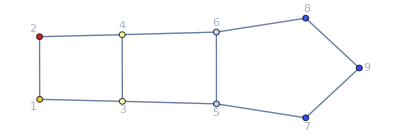

```mathematica
ColorNetworkByValueFunctionOperator[d2e][rule]
```

```mathematica
{timedata,d2e}=AbsoluteTiming[D2E[Data/.{I1-> 1,I2->2, U1-> 1,U2->2,U3->3}]];
timedata;
{time,{system,result}}=AbsoluteTiming@CriticalCongestionSolver[d2e];
time
```

1.4913

```mathematica
result=Solver[d2e][alpha=1];
```

The error (1-Norm of LHS-RHS) is 1.20737×10^-14

The error is 1.20737×10^-14 which is less than 1.×10^-10

It took 5.54414 seconds to solve!
	The system is True

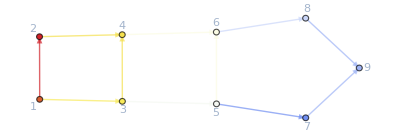

```mathematica
ColorNetworkByValueFunctionOperator[d2e][result]
```

```mathematica
d2e=D2E[Data/.{I1-> 2,I2->6, U1-> 1,U2->2,U3->0}];
{time,{system,rules}}=CriticalCongestionSolver[d2e]//AbsoluteTiming;
time
```

1.9647

```mathematica
{time,d2e}=AbsoluteTiming@D2E[Data/.{I1-> 2.00000000001515151515151515115151515115151515151551515151,I2->6, U1-> 3,U2->3,U3->0.}];
time
{time,{system,rules}}=CriticalCongestionSolver[d2e]//AbsoluteTiming;
time
```

0.102996

2.26777

#### Non-linear case

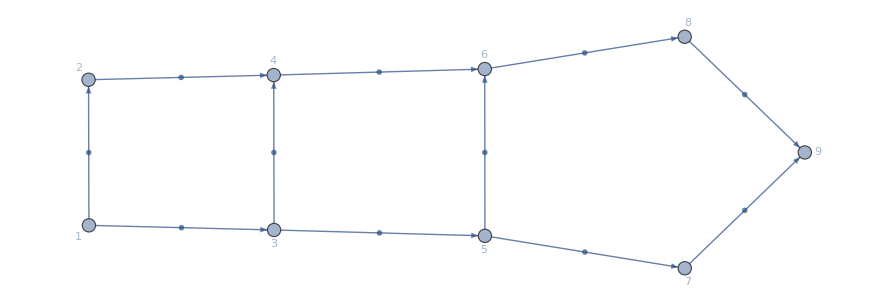

-Graphics-

```mathematica
(*Don't forget to change the Range!*)
alpha =1;
MFGEquations = d2e;
FFR=rules;
BEL=EdgeList[MFGEquations["BG"]];
pop=(#-> Plot[M[MFGEquations["jays"][#]/.FFR,x,#],{x,0,1}, (*PlotLabel->#,*)(*PlotRange->{-0.1,2.4},*)GridLines->Automatic,ImageSize->90])&/@BEL;
val=(#-> Plot[U[x, #, MFGEquations/.FFR],{x,0,1}, (*PlotLabel->#,*)(*PlotRange->{-0.1,4.7},*)GridLines->Automatic,ImageSize->90])&/@BEL;
Graph[MFGEquations["BG"],EdgeLabels-> pop,GraphLayout->"SpringElectricalEmbedding"]
Graph[MFGEquations["BG"],EdgeLabels-> val,GraphLayout->"SpringElectricalEmbedding"]
```

```mathematica
Solver[d2e][alpha = .1]
(*{timeFFR,FFR}= AbsoluteTiming[Catch@FixedPoint[FixedReduceX1[d2e1],rules1,200]//N//KeySort]*)
```

### The nonlinear solver solves the critical congestion case when the alpha is 1 and the initial currents are all zero.

```mathematica
rules0=AssociationThread[Values@d2e["jvars"],Table[0,{i,1,Length@d2e["jvars"]}]]
```

```mathematica
alpha = 1;
{timeFFR,FFR}= AbsoluteTiming@Catch@FixedPoint[FixedReduceX1[d2e],rules0, 1]
```

```mathematica
rules0=AssociationThread[Values @ d2e["jvars"],Table[0,{i,1,Length@d2e["jvars"]}]];
alpha = 1;
{timeFFR,FFR}= AbsoluteTiming@KeySort@Catch@FixedPoint[FixedReduceX1[d2e],rules0, 1]
d2e["EqCriticalCase"]/.FFR
```

### Test on a “large” network

#### D2E already takes half a minute. Set the option of giving the Graph with GridGraph, for example. Would this run faster?

Variables are all set

Assembled most elements of the system

{{u1≤u3,u1≤∞,u3≤u1,u3≤∞,u52≤u1,u52≤u3},{u2≤u5,u2≤u7,u5≤u2,u5≤u7,u7≤u2,u7≤u5},{u6≤u9,u6≤u11,u9≤u6,u9≤u11,u11≤u6,u11≤u9},{u10≤u13,u13≤u10},{u4≤u15,u4≤u17,u15≤u4,u15≤u17,u17≤u4,u17≤u15},{u8≤u16,u8≤u19,u8≤u21,u16≤u8,u16≤u19,u16≤u21,u19≤u8,u19≤u16,u19≤u21,u21≤u8,u21≤u16,u21≤u19},{u12≤u20,u12≤u23,u12≤u25,u20≤u12,u20≤u23,u20≤u25,u23≤u12,u23≤u20,u23≤u25,u25≤u12,u25≤u20,u25≤u23},{u14≤u24,u14≤u27,u24≤u14,u24≤u27,u27≤u14,u27≤u24},{u18≤u29,u18≤u31,u29≤u18,u29≤u31,u31≤u18,u31≤u29},{u22≤u30,u22≤u33,u22≤u35,u30≤u22,u30≤u33,u30≤u35,u33≤u22,u33≤u30,u33≤u35,u35≤u22,u35≤u30,u35≤u33},{u26≤u34,u26≤u37,u26≤u39,u34≤u26,u34≤u37,u34≤u39,u37≤u26,u37≤u34,u37≤u39,u39≤u26,u39≤u34,u39≤u37},{u28≤u38,u28≤u41,u38≤u28,u38≤u41,u41≤u28,u41≤u38},{u32≤u43,u43≤u32},{u36≤u44,u36≤u45,u44≤u36,u44≤u45,u45≤u36,u45≤u44},{u40≤u46,u40≤u47,u46≤u40,u46≤u47,u47≤u40,u47≤u46},{u42≤u48,u42≤u49,u48≤u42,u48≤u49,u49≤∞,u49≤∞}}

{u1==u3&&u3≥u52,u2==u7&&u5==u7,u11==u9&&u6==u9,u10==u13,u15==u17&&u17==u4,u16==u21&&u19==u8&&u21==u8,u12==u25&&u20==u25&&u23==u25,u14==u27&&u24==u27,u18==u31&&u29==u31,u22==u35&&u30==u35&&u33==u35,u26==u39&&u34==u39&&u37==u39,u28==u41&&u38==u41,u32==u43,u36==u45&&u44==u45,u40==u47&&u46==u47,u42==u48&&u48≤u49}

{u1==u3&&u3≥u52,u2==u7&&u5==u7,u11==u9&&u6==u9,u10==u13,u15==u17&&u17==u4,u16==u21&&u19==u8&&u21==u8,u12==u25&&u20==u25&&u23==u25,u14==u27&&u24==u27,u18==u31&&u29==u31,u22==u35&&u30==u35&&u33==u35,u26==u39&&u34==u39&&u37==u39,u28==u41&&u38==u41,u32==u43,u36==u45&&u44==u45,u40==u47&&u46==u47,u42==u48&&u48≤u49}

CleanEqualities for the switching conditions on each vertex

CleanEqualities for the complementary conditions (given the rules)

CleanEqualities for the values at the auxiliary edges

CleanEqualities for the balance conditions in terms of (mostly) transition currents

{{j30→-cpc11+cpc15-cpc8+cpc9-j15+j16+j17-j18-j21+j22+j29,j34→-cpc10+cpc11-cpc13+cpc17-j19+j20+j21-j22-j25+j26+j33,j38→-cpc12+cpc13-cpc14+cpc19-j23+j24+j25-j26-j27+j28+j37,j44→-cpc11+cpc16-cpc18+cpc22-cpc8+cpc9-j15+j16+j17-j18-j21+j22+j31-j32-j35+j36+j43,j46→-cpc10+cpc11-cpc13+cpc18-cpc20+cpc23-j19+j20+j21-j22-j25+j26+j35-j36-j39+j40+j45,j48→-cpc12+cpc13-cpc14+cpc20-cpc21+cpc24-j23+j24+j25-j26-j27+j28+j39-j40-j41+j42+j47,j6→cpc1-cpc10-cpc2+cpc3+cpc6-cpc8+j1+j11-j12-j15+j16-j19-j2+j20-j3+j4+j5,j8→cpc1-cpc2+cpc4-cpc8+j1-j15+j16-j2-j3+j4+j7,j9→cpc12-cpc5+cpc6-cpc7+j10+j11-j12-j13+j14+j23-j24,u10→cpc10+cpc12+cpc2-cpc7+cpc8-j13+j14+j15-j16+j19-j20+j23-j24+j3-j4+u1,u11→cpc10+cpc2-cpc6+cpc8-j11+j12+j15-j16+j19-j20+j3-j4+u1,u12→cpc10+cpc2+cpc8+j15-j16+j19-j20+j3-j4+u1,u14→cpc10+cpc12+cpc2+cpc8+j15-j16+j19-j20+j23-j24+j3-j4+u1,u15→cpc2+j3-j4+u1,u16→cpc2+cpc8+j15-j16+j3-j4+u1,u18→cpc2+cpc9+j17-j18+j3-j4+u1,u2→cpc1+j1-j2+u1,u22→cpc11+cpc2+cpc8+j15-j16+j21-j22+j3-j4+u1,u26→cpc10+cpc13+cpc2+cpc8+j15-j16+j19-j20+j25-j26+j3-j4+u1,u28→cpc10+cpc12+cpc14+cpc2+cpc8+j15-j16+j19-j20+j23-j24+j27-j28+j3-j4+u1,u32→cpc16+cpc2+cpc9+j17-j18+j3+j31-j32-j4+u1,u36→cpc11+cpc18+cpc2+cpc8+j15-j16+j21-j22+j3+j35-j36-j4+u1,u40→cpc10+cpc13+cpc2+cpc20+cpc8+j15-j16+j19-j20+j25-j26+j3+j39-j4-j40+u1,u42→cpc10+cpc12+cpc14+cpc2+cpc21+cpc8+j15-j16+j19-j20+j23-j24+j27-j28+j3-j4+j41-j42+u1}}

right?
{cpc1==0&&-j3+j4-u3+u4==0&&cpc1-cpc10-cpc2+cpc3+cpc6-cpc8+j1+j11-j12-j15+j16-j19-j2+j20-j3+j4-u5+u6==0&&cpc1-cpc2+cpc4-cpc8+j1-j15+j16-j2-j3+j4-u7+u8==0&&cpc10+cpc2+cpc5-cpc6+cpc8-j11+j12+j15-j16+j19-j20+j3-j4+u1-u9==0&&cpc6==0&&cpc10+cpc12+cpc2+cpc8-j13+j14+j15-j16+j19-j20+j23-j24+j3-j4+u1-u13==0&&cpc8==0&&cpc2+cpc9+j3-j4+u1-u17==0&&-j19+j20-u19+u20==0&&cpc11+cpc2+cpc8+j15-j16+j3-j4+u1-u21==0&&-j23+j24-u23+u24==0&&cpc10+cpc13+cpc2+cpc8+j15-j16+j19-j20+j3-j4+u1-u25==0&&cpc10+cpc12+cpc14+cpc2+cpc8+j15-j16+j19-j20+j23-j24+j3-j4+u1-u27==0&&-cpc11+cpc15-cpc8+cpc9-j15+j16+j17-j18-j21+j22-u29+u30==0&&cpc16+cpc2+cpc9+j17-j18+j3-j4+u1-u31==0&&-cpc10+cpc11-cpc13+cpc17-j19+j20+j21-j22-j25+j26-u33+u34==0&&cpc11+cpc18+cpc2+cpc8+j15-j16+j21-j22+j3-j4+u1-u35==0&&-cpc12+cpc13-cpc14+cpc19-j23+j24+j25-j26-j27+j28-u37+u38==0&&cpc10+cpc13+cpc2+cpc20+cpc8+j15-j16+j19-j20+j25-j26+j3-j4+u1-u39==0&&cpc10+cpc12+cpc14+cpc2+cpc21+cpc8+j15-j16+j19-j20+j23-j24+j27-j28+j3-j4+u1-u41==0&&-cpc11+cpc16-cpc18+cpc22-cpc8+cpc9-j15+j16+j17-j18-j21+j22+j31-j32-j35+j36-u43+u44==0&&-cpc10+cpc11-cpc13+cpc18-cpc20+cpc23-j19+j20+j21-j22-j25+j26+j35-j36-j39+j40-u45+u46==0&&-cpc12+cpc13-cpc14+cpc20-cpc21+cpc24-j23+j24+j25-j26-j27+j28+j39-j40-j41+j42-u47+u48==0}

CleanEqualities for the (non) critical case equations

EliminateVarsSimplify for the us

{u1==52/7&&u51==52/7,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,u1==u51,True}

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

Finished with the us!

Finish with the js

{j1==0,True,j3==0,True,j5==0,True,j7==0,True,True,j10==4/7,j11==0,True,j13==0,True,j15==0,True,j17==0,True,j19==0,True,j21==0,True,j23==0,True,j25==0,True,j27==0,True,j29==0,True,j31==0,True,j33==0,True,j35==0,True,j37==0,True,j39==0,True,j41==0,True,j43==0,True,j45==0,True,j47==0,True,True,True,True,True}

0.080038

systemgrid

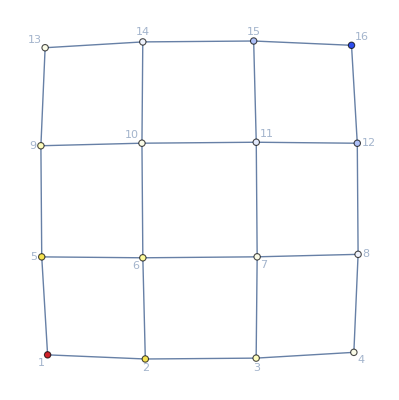

```mathematica
eme=4;
ege=4;
ete =1;
gr=GridGraph[{eme,ege,ete},DirectedEdges->True];
{timegridata,d2egrid}=AbsoluteTiming@D2E[
AssociationThread[{"Vertices List","Adjacency Matrix","Entrance Vertices and Currents","Exit Vertices and Terminal Costs","Switching Costs"}, {(*VL=*)VertexList[gr],(*AM=*)AdjacencyMatrix[gr],(*DataIn=*){{1,I1}/.I1->4},(*FinalCosts=*){{eme*ege*ete,U1}/.U1->0},(*SwitchingCostsData=*){}}]
];
{timegrid,rulesgrid}=CriticalCongestionSolver2[d2egrid]//AbsoluteTiming;
timegrid
systemgrid
ColorNetworkByValueFunctionOperator[d2egrid][rulesgrid]
```

```mathematica
Manipulate[eme=2;
ege=3;
ete =1;
gr=GridGraph[{eme,ege},DirectedEdges->True];
Datagrid =AssociationThread[{"Vertices List","Adjacency Matrix","Entrance Vertices and Currents","Exit Vertices and Terminal Costs","Switching Costs"}, {(*VL=*)VertexList[gr],(*AM=*)AdjacencyMatrix[gr],(*DataIn=*){{1,I1}/.I1->400},(*FinalCosts=*){{eme*ege*ete,U1}/.U1->0, {eme*ege*ete-1,0}, {eme*ege*ete-2,U2}},(*SwitchingCostsData=*){}}];
{timegridata,d2egrid}=AbsoluteTiming@D2E[Datagrid];
{timegrid,rulesgrid}=CriticalCongestionSolver2[d2egrid]//AbsoluteTiming;
Print[timegrid];
ColorNetworkByValueFunctionOperator[d2egrid][rulesgrid],{{U2,100},0,180,10}]
```

Variables are all set

Assembled most elements of the system

{{u1≤u3,u1≤∞,u3≤u1,u3≤∞,u52≤u1,u52≤u3},{u2≤u5,u2≤u7,u5≤u2,u5≤u7,u7≤u2,u7≤u5},{u6≤u9,u6≤u11,u9≤u6,u9≤u11,u11≤u6,u11≤u9},{u10≤u13,u10≤u15,u13≤u10,u13≤u15,u15≤u10,u15≤u13},{u14≤u17,u17≤u14},{u4≤u19,u4≤u21,u19≤u4,u19≤u21,u21≤u4,u21≤u19},{u8≤u20,u8≤u23,u8≤u25,u20≤u8,u20≤u23,u20≤u25,u23≤u8,u23≤u20,u23≤u25,u25≤u8,u25≤u20,u25≤u23},{u12≤u24,u12≤u27,u12≤u29,u24≤u12,u24≤u27,u24≤u29,u27≤u12,u27≤u24,u27≤u29,u29≤u12,u29≤u24,u29≤u27},{u16≤u28,u16≤u31,u16≤u33,u28≤u16,u28≤u31,u28≤u33,u31≤u16,u31≤u28,u31≤u33,u33≤u16,u33≤u28,u33≤u31},{u18≤u32,u18≤u35,u32≤u18,u32≤u35,u35≤u18,u35≤u32},{u22≤u37,u37≤u22},{u26≤u38,u26≤u39,u38≤u26,u38≤u39,u39≤u26,u39≤u38},{u30≤u40,u30≤u41,u30≤u43,u40≤u30,u40≤u41,u40≤u43,u41≤u30,u41≤u40,u41≤u43,u43≤∞,u43≤∞,u43≤∞},{u34≤u42,u34≤u45,u34≤u47,u42≤u34,u42≤u45,u42≤u47,u45≤u34,u45≤u42,u45≤u47,u47≤∞,u47≤∞,u47≤∞},{u36≤u46,u36≤u49,u46≤u36,u46≤u49,u49≤∞,u49≤∞}}

{u1==u3&&u3≥u52,u2==u7&&u5==u7,u11==u9&&u6==u9,u10==u15&&u13==u15,u14==u17,u19==u21&&u21==u4,u20==u25&&u23==u8&&u25==u8,u12==u29&&u24==u29&&u27==u29,u16==u33&&u28==u33&&u31==u33,u18==u35&&u32==u35,u22==u37,u26==u39&&u38==u39,u30==u41&&u40==u41&&u41≤u43,u34==u45&&u42==u45&&u45≤u47,u36==u46&&u46≤u49}

{u1==u3&&u3≥u52,u2==u7&&u5==u7,u11==u9&&u6==u9,u10==u15&&u13==u15,u14==u17,u19==u21&&u21==u4,u20==u25&&u23==u8&&u25==u8,u12==u29&&u24==u29&&u27==u29,u16==u33&&u28==u33&&u31==u33,u18==u35&&u32==u35,u22==u37,u26==u39&&u38==u39,u30==u41&&u40==u41&&u41≤u43,u34==u45&&u42==u45&&u45≤u47,u36==u46&&u46≤u49}

CleanEqualities for the switching conditions on each vertex

CleanEqualities for the complementary conditions (given the rules)

CleanEqualities for the values at the auxiliary edges

CleanEqualities for the balance conditions in terms of (mostly) transition currents

{{j32→cpc16-cpc7+cpc8-cpc9-j13+j14+j15-j16-j17+j18+j31,j38→-cpc10+cpc11-cpc13+cpc19-j19+j20+j21-j22-j25+j26+j37,j40→-cpc12+cpc13-cpc15+cpc20-j23+j24+j25-j26-j29+j30+j39,j42→-cpc14+cpc15-cpc17+cpc21-j27+j28+j29-j30-j33+j34+j41,j46→cpc17-cpc18+cpc22-cpc7+cpc8-cpc9-j13+j14+j15-j16-j17+j18+j33-j34-j35+j36+j45,j6→cpc1-cpc10-cpc12-cpc2+cpc3+cpc6+j1+j11-j12-j19-j2+j20-j23+j24-j3+j4+j5,j8→cpc1-cpc10-cpc2+cpc4+j1-j19-j2+j20-j3+j4+j7,j9→cpc14-cpc5+cpc6-cpc8+j10+j11-j12-j15+j16+j27-j28,u10→cpc10+cpc12+cpc14+cpc2-cpc8-j15+j16+j19-j20+j23-j24+j27-j28+j3-j4+u1,u11→cpc10+cpc12+cpc2-cpc6-j11+j12+j19-j20+j23-j24+j3-j4+u1,u12→cpc10+cpc12+cpc2+j19-j20+j23-j24+j3-j4+u1,u14→cpc10+cpc12+cpc14+cpc2+cpc7-cpc8+j13-j14-j15+j16+j19-j20+j23-j24+j27-j28+j3-j4+u1,u16→cpc10+cpc12+cpc14+cpc2+j19-j20+j23-j24+j27-j28+j3-j4+u1,u18→cpc10+cpc12+cpc14+cpc2+cpc7-cpc8+cpc9+j13-j14-j15+j16+j17-j18+j19-j20+j23-j24+j27-j28+j3-j4+u1,u19→cpc2+j3-j4+u1,u2→cpc1+j1-j2+u1,u20→cpc10+cpc2+j19-j20+j3-j4+u1,u22→cpc11+cpc2+j21-j22+j3-j4+u1,u26→cpc10+cpc13+cpc2+j19-j20+j25-j26+j3-j4+u1,u30→cpc10+cpc12+cpc15+cpc2+j19-j20+j23-j24+j29+j3-j30-j4+u1,u34→cpc10+cpc12+cpc14+cpc17+cpc2+j19-j20+j23-j24+j27-j28+j3+j33-j34-j4+u1,u36→cpc10+cpc12+cpc14+cpc18+cpc2+cpc7-cpc8+cpc9+j13-j14-j15+j16+j17-j18+j19-j20+j23-j24+j27-j28+j3+j35-j36-j4+u1}}

right?
{cpc1==0&&-j3+j4-u3+u4==0&&cpc1-cpc10-cpc12-cpc2+cpc3+cpc6+j1+j11-j12-j19-j2+j20-j23+j24-j3+j4-u5+u6==0&&cpc1-cpc10-cpc2+cpc4+j1-j19-j2+j20-j3+j4-u7+u8==0&&cpc10+cpc12+cpc2+cpc5-cpc6-j11+j12+j19-j20+j23-j24+j3-j4+u1-u9==0&&cpc6==0&&cpc10+cpc12+cpc14+cpc2+cpc7-cpc8-j15+j16+j19-j20+j23-j24+j27-j28+j3-j4+u1-u13==0&&cpc10+cpc12+cpc14+cpc2-j15+j16+j19-j20+j23-j24+j27-j28+j3-j4+u1-u15==0&&cpc10+cpc12+cpc14+cpc2+cpc7-cpc8+cpc9+j13-j14-j15+j16+j19-j20+j23-j24+j27-j28+j3-j4+u1-u17==0&&cpc10==0&&cpc11+cpc2+j3-j4+u1-u21==0&&-j23+j24-u23+u24==0&&cpc10+cpc13+cpc2+j19-j20+j3-j4+u1-u25==0&&-j27+j28-u27+u28==0&&cpc10+cpc12+cpc15+cpc2+j19-j20+j23-j24+j3-j4+u1-u29==0&&cpc16-cpc7+cpc8-cpc9-j13+j14+j15-j16-j17+j18-u31+u32==0&&cpc10+cpc12+cpc14+cpc17+cpc2+j19-j20+j23-j24+j27-j28+j3-j4+u1-u33==0&&cpc10+cpc12+cpc14+cpc18+cpc2+cpc7-cpc8+cpc9+j13-j14-j15+j16+j17-j18+j19-j20+j23-j24+j27-j28+j3-j4+u1-u35==0&&-cpc10+cpc11-cpc13+cpc19-j19+j20+j21-j22-j25+j26-u37+u38==0&&-cpc12+cpc13-cpc15+cpc20-j23+j24+j25-j26-j29+j30-u39+u40==0&&-cpc14+cpc15-cpc17+cpc21-j27+j28+j29-j30-j33+j34-u41+u42==0&&cpc17-cpc18+cpc22-cpc7+cpc8-cpc9-j13+j14+j15-j16-j17+j18+j33-j34-j35+j36-u45+u46==0}

CleanEqualities for the (non) critical case equations

EliminateVarsSimplify for the us

{jt101==-jt102-jt103+jt109+jt110&&jt27==-1050900/14101-jt32+jt33+jt34+jt35+jt37+jt38-jt39-jt42&&u1==141500/239&&u51==141500/239,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,u1==u51,True}

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

Finished with the us!

Finish with the js

{j1==0,True,j3==0,True,j5==0,True,j7==0,True,True,j10==1239200/14101,j11==0,True,j13==0,True,j15==0,True,j17==0,True,j19==0,True,j21==0,True,j23==0,True,j25==0,True,j27==0,True,j29==0,True,j31==0,True,j33==0,True,j35==0,True,j37==0,True,j39==0,True,j41==0,True,True,True,j45==0,True,True,True,True,True,True,True}

It took 0.181401 seconds to solve the critical congestion case.

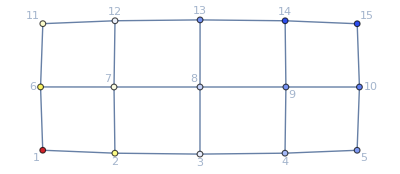

```mathematica
eme=5;
ege=3;
gr=GridGraph[{eme,ege},DirectedEdges->True];
Datagrid =AssociationThread[{"Vertices List","Adjacency Matrix","Entrance Vertices and Currents","Exit Vertices and Terminal Costs","Switching Costs"}, {(*VL=*)VertexList[gr],(*AM=*)AdjacencyMatrix[gr],(*DataIn=*){{1,I1}/.I1->400},(*FinalCosts=*){{eme*ege,U1}/.U1->0, {eme*ege-1,0}, {eme*ege-2,U2}/.U2->100},(*SwitchingCostsData=*){}}];
{timegridata,d2egrid}=AbsoluteTiming@D2E[Datagrid];
{timegrid,rulesgrid}=CriticalCongestionSolver2[d2egrid]//AbsoluteTiming;
Print["It took ",timegrid, " seconds to solve the critical congestion case."];
ColorNetworkByValueFunctionOperator[d2egrid][rulesgrid]
```

```mathematica
gr=GridGraph[{3,7},DirectedEdges->True, VertexLabels->"Name"];
Data =AssociationThread[{"Vertices List","Adjacency Matrix","Entrance Vertices and Currents","Exit Vertices and Terminal Costs","Switching Costs"}, {(*VL=*)VertexList[gr],(*AM=*)AdjacencyMatrix[gr],(*DataIn=*){{8,I1}/.I1->400},(*FinalCosts=*){{17,U1}/.U1->0},(*SwitchingCostsData=*){}}];
```

```mathematica
gr=GridGraph[{3,3},DirectedEdges->True];
Data =AssociationThread[{"Vertices List","Adjacency Matrix","Entrance Vertices and Currents","Exit Vertices and Terminal Costs","Switching Costs"}, {(*VL=*)VertexList[gr],(*AM=*)AdjacencyMatrix[gr],(*DataIn=*){{1,I1}/.I1->4,{3,4}},(*FinalCosts=*){{5,U1}/.U1->0(*,{8,0}*)},(*SwitchingCostsData=*){}}];
{timegridata,d2egrid}=AbsoluteTiming@D2E[Data];
alpha=1;
(rulesgrid = Solver[d2egrid][alpha]);
```

# TestZone

#### This is the winning code! Try this on CriticalCongestionSolverNewReduce

```mathematica
{system,rules}=((And@@(NewReduce/@(Select[system,Function[a,!FreeQ[a,#]]]&/@Values[d2egrid["uvars"]]))//Simplify)&&system)//CleanEqualities
```

# This is in the code already:

### Color representation of the value function (this is suitable for the critical congestion case because the value function is linear on each edge)

#### New function!!!

```mathematica
eStyle[colors_][pts_,DirectedEdge[x_,y_]]:={colors[[y]],Arrow[Line[pts,VertexColors->{colors[[x]],colors[[y]]}]]}

ColorNetworkByValueFunctionOperator[d2e1_Association][rules_]:= Module[{values,colors},
values=d2e1["VL"]/.KeyMap[#[[1]]&,d2e1["uvars"]/.rules];(*this works WITHOUT switching costs*)
(*Print[values];*)
colors=ColorData["TemperatureMap"]/@(values/Max[values]);
(*Print[colors];*)
GraphicsGrid[{
{HighlightGraph[SetProperty[d2e1["BG"],EdgeShapeFunction-> eStyle[colors]],Thread[Style[d2e1["VL"],colors]],GraphLayout->"SpringElectricalEmbedding"]},
{BarLegend["TemperatureMap",LegendMarkerSize->100,LegendLayout->"ReversedRow"]}
}]
]
```

### Idea:

```mathematica
eStyle[colors_][pts_,DirectedEdge[x_,y_]]:={colors[[y]],Arrow[Line[pts,VertexColors->{colors[[x]],colors[[y]]}]]}
g=GridGraph[{4,4},VertexLabels->"Name",ImagePadding->10,DirectedEdges->True];
colors=ColorData["TemperatureMap"]/@(VertexDegree[g]/Max[VertexDegree[g]]);
HighlightGraph[SetProperty[g,EdgeShapeFunction->eStyle[colors]],Thread[Style[VertexList[g],colors]]]
```